# A mathematical model for universal semantics (Text mining in French)

### Weinan E and Yajun Zhou

## Introduction

Accompanying the topic extraction and word translation sections in [1], this Mathematica Notebook file is optimized for v11.0, and it will also run on v10.3 and v10.4. Earlier versions of Mathematica do not contain certain text analysis functionalities required for this program.

Unless explicitly stated otherwise, all the routines (word clustering, word cloud plotting and question answering) below are specifically designed for the current work [1], instead of being imported elsewhere.

[1] W. E and Y. Zhou, “A mathematical model for universal semantics,” 2020, arXiv:1907.12293v6 [cs.CL].

## Preparations

Text corpora mentioned below need to be stored in the following directory (or anywhere else that you redesignate)

```mathematica
SetDirectory["D:\\Documents"]
```

D:\Documents

This Mathematica Notebook file MUST BE executed AFTER all the cells in English.nb are evaluated.

### Pride and Prejudice

The full text for a French translation of Jane Austen’s Pride and Prejudice is freely available from https://fr.wikisource.org/wiki/Les_Cinq_Filles_de_Mrs_Bennet/Texte_entier

After manual cleansing, we save the text as Les cinq filles de Mrs Bennet (Leconte-Pressoir).txt,  which begins with

"I C’est une vérité universellement reconnue qu’un célibataire pourvu d’une belle fortune doit avoir envie de se marier, et, si peu que l’on sache de son sentiment à cet égard, lorsqu’il arrive dans un"

and ends with

"x une affection réelle ; et tous deux conservèrent toujours la plus vive reconnaissance pour ceux qui, en amenant Elizabeth en Derbyshire, avaient joué entre eux le rôle providentiel de trait d’union."

The current Mathematica Notebook demonstrates the analysis of Pride and Prejudice. For the analysis of other texts in our current work, one needs to download text corpora and modify the codes slightly.

### Jane Eyre

The full text  for a French translation of Charlotte Brontë’s Jane Eyre is freely available from http://www.gutenberg.org/cache/epub/16235/pg16235.txt

After manual cleansing, the text begins with

"CHAPITRE PREMIER Il était impossible de se promener ce jour-là. Le matin, nous avions erré pendant une heure dans le bosquet dépouillé de feuilles; mais, depuis le dîner (quand il n'y avait personne, "

and ends with

"n maître, dit-il, m'a averti; chaque jour il m'annonce plus clairement ma délivrance. J'avance rapidement, et à chaque heure qui s'écoule, je réponds avec plus d'ardeur; «Amen; venez, Seigneur Jésus!»"

### Origin of Species

The full text  for a French translation of Charles Darwin’s Origin of Species is freely available from http://www.gutenberg.org/cache/epub/14158/pg14158.txt

After manual cleansing, the text begins with

CHAPITRE I
DE LA VARIATION DES ESPÈCES À L'ÉTAT DOMESTIQUE

_Causes de la variabilité. -- Effets des habitudes. -- Effets de
l'usage ou du non-usage des parties. -- Variation par corrélation.
-- Héréd

and ends with

gravitation, continue à tourner dans son orbite, une quantité
infinie de belles et admirables formes, sorties d'un commencement
si simple, n'ont pas cessé de se développer et se développent
encore!

Making sure that all the cells in English.nb have been evaluated, you are ready to execute all the cells in this file.

## French

## French sample words

Unlike Spanish, French verb conjugations do not exhibit systematic vowel alternations. In fact, the vowels in almost all French verb stems are invariant. There are a few dozen commonly used French verbs that are irregular in their own unique ways. They need to be treated carefully in word clustering algorithms.

French verbs are divided into three conjugation groups. The first two groups are “regular”, while the verbs in the third group are all irregular. Unlike Spanish regular verbs, the root of a verb in the first two conjugations in French sometimes may undergo cosmetic changes for phonological reasons — their counterparts in Spanish would be classified as “irregular”, but we adhere to the traditional French grammar (as in https://en.wiktionary.org/wiki/Appendix:French_verbs) below, and include them as exceptional cases of the first two “regular” conjugations in French. Similar to the sampling of Spanish verbs, we ignore cases where the French verb root is different by at most a diacritic mark on the letter e (as both é and è will be converted to e in the effective spelling) in conjugated forms.

```mathematica
loveFrench={"aima","aimai","aimaient","aimais","aimait","aimâmes","aimant","aimas","aimasse","aimassent","aimasses","aimassiez","aimassions","aimât","aimâtes","aime","aimé","aiment","aimer","aimera","aimerai","aimeraient","aimerais","aimerait","aimeras","aimèrent","aimerez","aimeriez","aimerions","aimerons","aimeront","aimes","aimez","aimiez","aimions","aimons"};
```

```mathematica
placeFrench={"plaça","plaçai","plaçaient","plaçais","plaçait","plaçâmes","plaçant","plaças","plaçasse","plaçassent","plaçasses","plaçassiez","plaçassions","plaçât","plaçâtes","place","placé","placent","placer","placera","placerai","placeraient","placerais","placerait","placeras","placèrent","placerez","placeriez","placerions","placerons","placeront","places","placez","placiez","placions","plaçons"};
```

```mathematica
eatFrench={"mange","mangé","mangea","mangeai","mangeaient","mangeais","mangeait","mangeâmes","mangeant","mangeas","mangeasse","mangeassent","mangeasses","mangeassiez","mangeassions","mangeât","mangeâtes","mangent","mangeons","manger","mangera","mangerai","mangeraient","mangerais","mangerait","mangeras","mangèrent","mangerez","mangeriez","mangerions","mangerons","mangeront","manges","mangez","mangiez","mangions"};
```

```mathematica
callFrench={"appela","appelai","appelaient","appelais","appelait","appelâmes","appelant","appelas","appelasse","appelassent","appelasses","appelassiez","appelassions","appelât","appelâtes","appelé","appeler","appelèrent","appelez","appeliez","appelions","appelle","appellent","appellera","appellerai","appelleraient","appellerais","appellerait","appelleras","appellerez","appelleriez","appellerions","appellerons","appelleront","appelles","appelons"};
```

```mathematica
drownFrench={"noie","noient","noiera","noierai","noieraient","noierais","noierait","noieras","noierez","noieriez","noierions","noierons","noieront","noies","noya","noyai","noyaient","noyais","noyait","noyâmes","noyant","noyas","noyasse","noyassent","noyasses","noyassiez","noyassions","noyât","noyâtes","noyé","noyer","noyèrent","noyez","noyiez","noyions","noyons"};
```

```mathematica
payFrench={"paie","paient","paiera","paierai","paieraient","paierais","paierait","paieras","paierez","paieriez","paierions","paierons","paieront","paies","paya","payai","payaient","payais","payait","payâmes","payant","payas","payasse","payassent","payasses","payassiez","payassions","payât","payâtes","paye","payé","payent","payer","payera","payerai","payeraient","payerais","payerait","payeras","payèrent","payerez","payeriez","payerions","payerons","payeront","payes","payez","payiez","payions","payons"};
```

```mathematica
createFrench={"créa","créai","créaient","créais","créait","créâmes","créant","créas","créasse","créassent","créasses","créassiez","créassions","créât","créâtes","crée","créé","créent","créer","créera","créerai","créeraient","créerais","créerait","créeras","créèrent","créerez","créeriez","créerions","créerons","créeront","crées","créez","créiez","créions","créons"};
```

```mathematica
finishFrench={"fini","finîmes","finir","finira","finirai","finiraient","finirais","finirait","finiras","finirent","finirez","finiriez","finirions","finirons","finiront","finis","finissaient","finissais","finissait","finissant","finisse","finissent","finisses","finissez","finissiez","finissions","finissons","finit","finît","finîtes"};
```

```mathematica
hateFrench={"haï","haïmes","haïr","haïra","haïrai","haïraient","haïrais","haïrait","haïras","haïrent","haïrez","haïriez","haïrions","haïrons","haïront","hais","haïs","haïssaient","haïssais","haïssait","haïssant","haïsse","haïssent","haïsses","haïssez","haïssiez","haïssions","haïssons","hait","haït","haïtes"};
```

```mathematica
FrenchSampleRegularVerbs=loveFrench∪placeFrench∪eatFrench∪callFrench∪drownFrench∪payFrench∪createFrench∪finishFrench∪hateFrench;
```

The samples of French irregular verbs (all from the third conjugation) below follow the classfication scheme in Wiktionary (https://en.wiktionary.org/wiki/Appendix:French_irregular_verbs).

```mathematica
sendFrench={"enverra","enverrai","enverraient","enverrais","enverrait","enverras","enverrez","enverriez","enverrions","enverrons","enverront","envoie","envoient","envoies","envoya","envoyai","envoyaient","envoyais","envoyait","envoyâmes","envoyant","envoyas","envoyasse","envoyassent","envoyasses","envoyassiez","envoyassions","envoyât","envoyâtes","envoyé","envoyer","envoyèrent","envoyez","envoyiez","envoyions","envoyons"};
```

```mathematica
gatherFrench={"cueillaient","cueillais","cueillait","cueillant","cueille","cueillent","cueillera","cueillerai","cueilleraient","cueillerais","cueillerait","cueilleras","cueillerez","cueilleriez","cueillerions","cueillerons","cueilleront","cueilles","cueillez","cueilli","cueilliez","cueillîmes","cueillions","cueillir","cueillirent","cueillis","cueillisse","cueillissent","cueillisses","cueillissiez","cueillissions","cueillit","cueillît","cueillîtes","cueillons"};
```

```mathematica
assailFrench={"assaillaient","assaillais","assaillait","assaillant","assaille","assaillé","assaillent","assailles","assaillez","assailliez","assaillîmes","assaillions","assaillir","assaillira","assaillirai","assailliraient","assaillirais","assaillirait","assailliras","assaillirent","assaillirez","assailliriez","assaillirions","assaillirons","assailliront","assaillis","assaillisse","assaillissent","assaillisses","assaillissiez","assaillissions","assaillit","assaillît","assaillîtes","assaillons"};
```

```mathematica
offerFrench={"offert","offraient","offrais","offrait","offrant","offre","offrent","offres","offrez","offriez","offrîmes","offrions","offrir","offrira","offrirai","offriraient","offrirais","offrirait","offriras","offrirent","offrirez","offririez","offririons","offrirons","offriront","offris","offrisse","offrissent","offrisses","offrissiez","offrissions","offrit","offrît","offrîtes","offrons"};
```

```mathematica
sleepFrench={"dormaient","dormais","dormait","dormant","dorme","dorment","dormes","dormez","dormi","dormiez","dormîmes","dormions","dormir","dormira","dormirai","dormiraient","dormirais","dormirait","dormiras","dormirent","dormirez","dormiriez","dormirions","dormirons","dormiront","dormis","dormisse","dormissent","dormisses","dormissiez","dormissions","dormit","dormît","dormîtes","dormons","dors","dort"};
```

```mathematica
boilFrench={"bouillaient","bouillais","bouillait","bouillant","bouille","bouillent","bouilles","bouillez","bouilli","bouilliez","bouillîmes","bouillions","bouillira","bouillirai","bouilliraient","bouillirais","bouillirait","bouilliras","bouillirent","bouillirez","bouilliriez","bouillirions","bouillirons","bouilliront","bouillis","bouillisse","bouillissent","bouillisses","bouillissiez","bouillissions","bouillit","bouillît","bouillîtes","bouillons","bous","bout"};
```

```mathematica
dressFrench={"vêt","vêtaient","vêtais","vêtait","vêtant","vête","vêtent","vêtes","vêtez","vêtiez","vêtîmes","vêtions","vêtir","vêtira","vêtirai","vêtiraient","vêtirais","vêtirait","vêtiras","vêtirent","vêtirez","vêtiriez","vêtirions","vêtirons","vêtiront","vêtis","vêtisse","vêtissent","vêtisses","vêtissiez","vêtissions","vêtit","vêtît","vêtîtes","vêtons","vêts","vêtu"};
```

```mathematica
runFrench={"couraient","courais","courait","courant","coure","courent","coures","courez","couriez","courions","courir","courons","courra","courrai","courraient","courrais","courrait","courras","courrez","courriez","courrions","courrons","courront","cours","court","couru","courûmes","coururent","courus","courusse","courussent","courusses","courussiez","courussions","courut","courût","courûtes"};
```

```mathematica
acquireFrench={"acquéraient","acquérais","acquérait","acquérant","acquérez","acquériez","acquérions","acquérir","acquérons","acquerra","acquerrai","acquerraient","acquerrais","acquerrait","acquerras","acquerrez","acquerriez","acquerrions","acquerrons","acquerront","acquière","acquièrent","acquières","acquiers","acquiert","acquîmes","acquirent","acquis","acquisse","acquissent","acquisses","acquissiez","acquissions","acquit","acquît","acquîtes"};
```

```mathematica
dieFrench={"meure","meurent","meures","meurs","meurt","mort","mouraient","mourais","mourait","mourant","mourez","mouriez","mourions","mourir","mourons","mourra","mourrai","mourraient","mourrais","mourrait","mourras","mourrez","mourriez","mourrions","mourrons","mourront","mourûmes","moururent","mourus","mourusse","mourussent","mourusses","mourussiez","mourussions","mourut","mourût","mourûtes"};
```

```mathematica
escapeFrench={"fui","fuie","fuient","fuies","fuîmes","fuir","fuira","fuirai","fuiraient","fuirais","fuirait","fuiras","fuirent","fuirez","fuiriez","fuirions","fuirons","fuiront","fuis","fuisse","fuissent","fuisses","fuissiez","fuissions","fuit","fuît","fuîtes","fuyaient","fuyais","fuyait","fuyant","fuyez","fuyiez","fuyions","fuyons"};
```

```mathematica
canFrench={"peut","peuvent","peux","pourra","pourrai","pourraient","pourrais","pourrait","pourras","pourrez","pourriez","pourrions","pourrons","pourront","pouvaient","pouvais","pouvait","pouvant","pouvez","pouviez","pouvions","pouvoir","pouvons","pu","puisse","puissent","puisses","puissiez","puissions","pûmes","purent","pus","pusse","pussent","pusses","pussiez","pussions","put","pût","pûtes"};
```

```mathematica
wishFrench={"veuille","veuillent","veuilles","veulent","veut","veux","voudra","voudrai","voudraient","voudrais","voudrait","voudras","voudrez","voudriez","voudrions","voudrons","voudront","voulaient","voulais","voulait","voulant","voulez","vouliez","voulions","vouloir","voulons","voulu","voulûmes","voulurent","voulus","voulusse","voulussent","voulusses","voulussiez","voulussions","voulut","voulût","voulûtes"};
```

```mathematica
moveFrench={"meus","meut","meuve","meuvent","meuves","mouvaient","mouvais","mouvait","mouvant","mouvez","mouviez","mouvions","mouvoir","mouvons","mouvra","mouvrai","mouvraient","mouvrais","mouvrait","mouvras","mouvrez","mouvriez","mouvrions","mouvrons","mouvront","mû","mûmes","murent","mus","musse","mussent","musses","mussiez","mussions","mut","mût","mûtes"};
```

```mathematica
receiveFrench={"recevaient","recevais","recevait","recevant","recevez","receviez","recevions","recevoir","recevons","recevra","recevrai","recevraient","recevrais","recevrait","recevras","recevrez","recevriez","recevrions","recevrons","recevront","reçois","reçoit","reçoive","reçoivent","reçoives","reçu","reçûmes","reçurent","reçus","reçusse","reçussent","reçusses","reçussiez","reçussions","reçut","reçût","reçûtes"};
```

```mathematica
knowFrench={"sachant","sache","sachent","saches","sachez","sachiez","sachions","sachons","sais","sait","saura","saurai","sauraient","saurais","saurait","sauras","saurez","sauriez","saurions","saurons","sauront","savaient","savais","savait","savent","savez","saviez","savions","savoir","savons","su","sûmes","surent","sus","susse","sussent","susses","sussiez","sussions","sut","sût","sûtes"};
```

```mathematica
earnFrench={"vaille","vaillent","vailles","valaient","valais","valait","valant","valent","valez","valiez","valions","valoir","valons","valu","valûmes","valurent","valus","valusse","valussent","valusses","valussiez","valussions","valut","valût","valûtes","vaudra","vaudrai","vaudraient","vaudrais","vaudrait","vaudras","vaudrez","vaudriez","vaudrions","vaudrons","vaudront","vaut","vaux"};
```

```mathematica
sayFrench={"dîmes","dira","dirai","diraient","dirais","dirait","diras","dire","dirent","direz","diriez","dirions","dirons","diront","dis","disaient","disais","disait","disant","dise","disent","dises","disiez","disions","disons","disse","dissent","disses","dissiez","dissions","dit","dît","dites","dîtes"};
```

```mathematica
sitFrench={"asseoir","asseyaient","asseyais","asseyait","asseyant","asseye","asseyent","asseyes","asseyez","asseyiez","asseyions","asseyons","assied","assieds","assiéra","assiérai","assiéraient","assiérais","assiérait","assiéras","assiérez","assiériez","assiérions","assiérons","assiéront","assîmes","assirent","assis","assisse","assissent","assisses","assissiez","assissions","assit","assît","assîtes","assoie","assoient","assoies","assoira","assoirai","assoiraient","assoirais","assoirait","assoiras","assoirez","assoiriez","assoirions","assoirons","assoiront","assois","assoit","assoyaient","assoyais","assoyait","assoyant","assoyez","assoyiez","assoyions","assoyons"};
```

```mathematica
waneFrench={"décherra","décherrai","décherraient","décherrais","décherrait","décherras","décherrez","décherriez","décherrions","décherrons","décherront","déchet","déchoie","déchoient","déchoies","déchoir","déchoira","déchoirai","déchoiraient","déchoirais","déchoirait","déchoiras","déchoirez","déchoiriez","déchoirions","déchoirons","déchoiront","déchois","déchoit","déchoyant","déchoyez","déchoyiez","déchoyions","déchoyons","déchu","déchûmes","déchurent","déchus","déchusse","déchussent","déchusses","déchussiez","déchussions","déchut","déchût","déchûtes"};
```

```mathematica
fearFrench={"craignaient","craignais","craignait","craignant","craigne","craignent","craignes","craignez","craigniez","craignîmes","craignions","craignirent","craignis","craignisse","craignissent","craignisses","craignissiez","craignissions","craignit","craignît","craignîtes","craignons","craindra","craindrai","craindraient","craindrais","craindrait","craindras","craindre","craindrez","craindriez","craindrions","craindrons","craindront","crains","craint"};
```

```mathematica
paintFrench={"peignaient","peignais","peignait","peignant","peigne","peignent","peignes","peignez","peigniez","peignîmes","peignions","peignirent","peignis","peignisse","peignissent","peignisses","peignissiez","peignissions","peignit","peignît","peignîtes","peignons","peindra","peindrai","peindraient","peindrais","peindrait","peindras","peindre","peindrez","peindriez","peindrions","peindrons","peindront","peins","peint"};
```

```mathematica
joinFrench={"joignaient","joignais","joignait","joignant","joigne","joignent","joignes","joignez","joigniez","joignîmes","joignions","joignirent","joignis","joignisse","joignissent","joignisses","joignissiez","joignissions","joignit","joignît","joignîtes","joignons","joindra","joindrai","joindraient","joindrais","joindrait","joindras","joindre","joindrez","joindriez","joindrions","joindrons","joindront","joins","joint"};
```

```mathematica
dissolveFrench={"dissolûmes","dissolurent","dissolus","dissolut","dissolûtes","dissolvaient","dissolvais","dissolvait","dissolvant","dissolve","dissolvent","dissolves","dissolvez","dissolviez","dissolvions","dissolvons","dissoudra","dissoudrai","dissoudraient","dissoudrais","dissoudrait","dissoudras","dissoudre","dissoudrez","dissoudriez","dissoudrions","dissoudrons","dissoudront","dissous","dissout"};
```

```mathematica
beatFrench={"bat","bats","battaient","battais","battait","battant","batte","battent","battes","battez","battiez","battîmes","battions","battirent","battis","battisse","battissent","battisses","battissiez","battissions","battit","battît","battîtes","battons","battra","battrai","battraient","battrais","battrait","battras","battre","battrez","battriez","battrions","battrons","battront","battu"};
```

```mathematica
sewFrench={"coud","coudra","coudrai","coudraient","coudrais","coudrait","coudras","coudre","coudrez","coudriez","coudrions","coudrons","coudront","couds","cousaient","cousais","cousait","cousant","couse","cousent","couses","cousez","cousiez","cousîmes","cousions","cousirent","cousis","cousisse","cousissent","cousisses","cousissiez","cousissions","cousit","cousît","cousîtes","cousons","cousu"};
```

```mathematica
grindFrench={"moud","moudra","moudrai","moudraient","moudrais","moudrait","moudras","moudre","moudrez","moudriez","moudrions","moudrons","moudront","mouds","moulaient","moulais","moulait","moulant","moule","moulent","moules","moulez","mouliez","moulions","moulons","moulu","moulûmes","moulurent","moulus","moulusse","moulussent","moulusses","moulussiez","moulussions","moulut","moulût","moulûtes"};
```

```mathematica
winFrench={"vainc","vaincra","vaincrai","vaincraient","vaincrais","vaincrait","vaincras","vaincre","vaincrez","vaincriez","vaincrions","vaincrons","vaincront","vaincs","vaincu","vainquaient","vainquais","vainquait","vainquant","vainque","vainquent","vainques","vainquez","vainquiez","vainquîmes","vainquions","vainquirent","vainquis","vainquisse","vainquissent","vainquisses","vainquissiez","vainquissions","vainquit","vainquît","vainquîtes","vainquons"};
```

```mathematica
liveFrench={"vécu","vécûmes","vécurent","vécus","vécusse","vécussent","vécusses","vécussiez","vécussions","vécut","vécût","vécûtes","vis","vit","vivaient","vivais","vivait","vivant","vive","vivent","vives","vivez","viviez","vivions","vivons","vivra","vivrai","vivraient","vivrais","vivrait","vivras","vivre","vivrez","vivriez","vivrions","vivrons","vivront"};
```

```mathematica
bebornFrench={"nais","naissaient","naissais","naissait","naissant","naisse","naissent","naisses","naissez","naissiez","naissions","naissons","naît","naîtra","naîtrai","naîtraient","naîtrais","naîtrait","naîtras","naître","naîtrez","naîtriez","naîtrions","naîtrons","naîtront","naquîmes","naquirent","naquis","naquisse","naquissent","naquisses","naquissiez","naquissions","naquit","naquît","naquîtes","né"};
```

```mathematica
increaseFrench={"accrois","accroissaient","accroissais","accroissait","accroissant","accroisse","accroissent","accroisses","accroissez","accroissiez","accroissions","accroissons","accroît","accroîtra","accroîtrai","accroîtraient","accroîtrais","accroîtrait","accroîtras","accroître","accroîtrez","accroîtriez","accroîtrions","accroîtrons","accroîtront","accrû","accrûmes","accrûrent","accrûs","accrûsse","accrûssent","accrûsses","accrûssiez","accrûssions","accrût","accrûtes"};
```

```mathematica
spoilFrench={"nui","nuira","nuirai","nuiraient","nuirais","nuirait","nuiras","nuire","nuirez","nuiriez","nuirions","nuirons","nuiront","nuis","nuisaient","nuisais","nuisait","nuisant","nuise","nuisent","nuises","nuisez","nuisiez","nuisîmes","nuisions","nuisirent","nuisis","nuisisse","nuisissent","nuisisses","nuisissiez","nuisissions","nuisit","nuisît","nuisîtes","nuisons","nuit"};
```

```mathematica
concludeFrench={"conclu","concluaient","concluais","concluait","concluant","conclue","concluent","conclues","concluez","concluiez","concluions","conclûmes","concluons","conclura","conclurai","concluraient","conclurais","conclurait","concluras","conclure","conclurent","conclurez","concluriez","conclurions","conclurons","concluront","conclus","conclusse","conclussent","conclusses","conclussiez","conclussions","conclut","conclût","conclûtes"};
```

```mathematica
includeFrench={"incluaient","incluais","incluait","incluant","inclue","incluent","inclues","incluez","incluiez","incluions","inclûmes","incluons","inclura","inclurai","incluraient","inclurais","inclurait","incluras","inclure","inclurent","inclurez","incluriez","inclurions","inclurons","incluront","inclus","inclusse","inclussent","inclusses","inclussiez","inclussions","inclut","inclût","inclûtes"};
```

```mathematica
believeFrench={"croie","croient","croies","croira","croirai","croiraient","croirais","croirait","croiras","croire","croirez","croiriez","croirions","croirons","croiront","crois","croit","croyaient","croyais","croyait","croyant","croyez","croyiez","croyions","croyons","cru","crûmes","crurent","crus","crusse","crussent","crusses","crussiez","crussions","crut","crût","crûtes"};
```

```mathematica
brayFrench={"braie","braient","braies","braira","brairai","brairaient","brairais","brairait","brairas","braire","brairez","brairiez","brairions","brairons","brairont","brais","brait","braya","brayai","brayaient","brayais","brayait","brayâmes","brayant","brayas","brayasse","brayassent","brayasses","brayassiez","brayassions","brayât","brayâtes","brayèrent","brayez","brayiez","brayions","brayons"};
```

```mathematica
pleaseFrench={"plaira","plairai","plairaient","plairais","plairait","plairas","plaire","plairez","plairiez","plairions","plairons","plairont","plais","plaisaient","plaisais","plaisait","plaisant","plaise","plaisent","plaises","plaisez","plaisiez","plaisions","plaisons","plait","plaît","plu","plûmes","plurent","plus","plusse","plussent","plusses","plussiez","plussions","plut","plût","plûtes"};
```

```mathematica
milkFrench={"traie","traient","traies","traira","trairai","trairaient","trairais","trairait","trairas","traire","trairez","trairiez","trairions","trairons","trairont","trais","trait","traya","trayai","trayaient","trayais","trayait","trayâmes","trayant","trayas","trayasse","trayassent","trayasses","trayassiez","trayassions","trayât","trayâtes","trayèrent","trayez","trayiez","trayions","trayons"};
```

```mathematica
hatchFrench={"éclora","éclorai","écloraient","éclorais","éclorait","écloras","éclore","éclorez","écloriez","éclorions","éclorons","écloront","éclos","éclosant","éclose","éclosent","écloses","éclosez","éclosiez","éclosions","éclosons","éclôt"};
```

```mathematica
sufficeFrench={"suffi","suffîmes","suffira","suffirai","suffiraient","suffirais","suffirait","suffiras","suffire","suffirent","suffirez","suffiriez","suffirions","suffirons","suffiront","suffis","suffisaient","suffisais","suffisait","suffisant","suffise","suffisent","suffises","suffisez","suffisiez","suffisions","suffisons","suffisse","suffissent","suffisses","suffissiez","suffissions","suffit","suffît","suffîtes"};
```

```mathematica
laughFrench={"riaient","riais","riait","riant","rie","rient","ries","riez","riiez","riions","rîmes","rions","rira","rirai","riraient","rirais","rirait","riras","rire","rirent","rirez","ririez","ririons","rirons","riront","ris","risse","rissent","risses","rissiez","rissions","rit","rît","rîtes"};
```

```mathematica
writeFrench={"écrira","écrirai","écriraient","écrirais","écrirait","écriras","écrire","écrirez","écririez","écririons","écrirons","écriront","écris","écrit","écrivaient","écrivais","écrivait","écrivant","écrive","écrivent","écrives","écrivez","écriviez","écrivîmes","écrivions","écrivirent","écrivis","écrivisse","écrivissent","écrivisses","écrivissiez","écrivissions","écrivit","écrivît","écrivîtes","écrivons"};
```

```mathematica
readFrench={"lira","lirai","liraient","lirais","lirait","liras","lire","lirez","liriez","lirions","lirons","liront","lis","lisaient","lisais","lisait","lisant","lise","lisent","lises","lisez","lisiez","lisions","lisons","lit","lu","lûmes","lurent","lus","lusse","lussent","lusses","lussiez","lussions","lut","lût","lûtes"};
```

```mathematica
takeFrench={"prenaient","prenais","prenait","prenant","prend","prendra","prendrai","prendraient","prendrais","prendrait","prendras","prendre","prendrez","prendriez","prendrions","prendrons","prendront","prends","prenez","preniez","prenions","prenne","prennent","prennes","prenons","prîmes","prirent","pris","prisse","prissent","prisses","prissiez","prissions","prit","prît","prîtes"};
```

```mathematica
FrenchSampleIrregularVerbs=sendFrench∪gatherFrench∪assailFrench∪offerFrench∪sleepFrench∪boilFrench∪dressFrench∪runFrench∪acquireFrench∪dieFrench∪escapeFrench∪wishFrench∪moveFrench∪receiveFrench∪knowFrench∪earnFrench∪sayFrench∪sitFrench∪waneFrench∪fearFrench∪paintFrench∪joinFrench∪dissolveFrench∪beatFrench∪sewFrench∪grindFrench∪winFrench∪liveFrench∪bebornFrench∪increaseFrench∪spoilFrench∪concludeFrench∪includeFrench∪believeFrench∪brayFrench∪pleaseFrench∪milkFrench∪hatchFrench∪sufficeFrench∪laughFrench∪writeFrench∪readFrench∪takeFrench;
```

## Approximate clustering of French words

The clustering routine is described below.

### Effective spelling and essential root

```mathematica
comeFrench={"venaient","venais","venait","venant","venez","veniez","venions","venir","venons","venu","viendra","viendrai","viendraient","viendrais","viendrait","viendras","viendrez","viendriez","viendrions","viendrons","viendront","vienne","viennent","viennes","viens","vient","vînmes","vinrent","vins","vinsse","vinssent","vinsses","vinssiez","vinssions","vint","vînt","vîntes"}∪{"venus"};
```

```mathematica
goFrench={"aille","ailles","aillent","alla","allai","allaient","allais","allait","allâmes","allant","allas","allasse","allassent","allasses","allassiez","allassions","allât","allâtes","allé","aller","allèrent","allez","alliez","allions","allons","ira","irai","iraient","irais","irait","iras","irez","iriez","irions","irons","iront","va","vais","vas","vont"}∪{"allés"};
```

```mathematica
yellFrench={"écria","écriai","écriaient","écriais","écriait","écriâmes","écriant","écrias","écriasse","écriassent","écriasses","écriassiez","écriassions","écriât","écriâtes","écrie","écrié","écrient","écrier","écriera","écrierai","écrieraient","écrierais","écrierait","écrieras","écrièrent","écrierez","écrieriez","écrierions","écrierons","écrieront","écries","écriez","écriiez","écriions","écrions"};
```

```mathematica
FrenchEffVowels="a"|"â"|"e"|"ê"|"i"|"î"|"o"|"u"|"û";
```

```mathematica
FrenchEffSpell[w_]:=StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[w,{WordBoundary~~"bessie"~~WordBoundary:>"βeσθie",WordBoundary~~"partag":>"paρτag",WordBoundary~~"hui"~~WordBoundary:>"αujourδ",WordBoundary~~"triste":>"triστe",WordBoundary~~"nom":>"noμ",WordBoundary~~"chance":>"ßance",WordBoundary~~"term":>"terμ",WordBoundary~~"guid":>"γuid",WordBoundary~~"guet":>"γuϵt",WordBoundary~~"message":>"μeßage",WordBoundary~~"ô":>"wô",WordBoundary~~"vie"~~""|"s"~~WordBoundary:>"vivre",WordBoundary~~"trois":>"3trois","ndité"~~___:>"nd","inct"~~___:>"ingue","récemment":>"récent",WordBoundary~~"nu"~~"e"|""~~"s"|""~~WordBoundary:>"νuδϵ","quotidien"~~___:>"jour","charlotte":>"chaρλωτ",WordBoundary~~"mme"~~""|"s"~~WordBoundary:>"lady",WordBoundary~~""|"ma"|"mes"~~"dame"~~""|"s"~~WordBoundary:>"lady",WordBoundary~~"mlle"~~""|"s"~~WordBoundary:>"miß",WordBoundary~~""|"ma"|"mes"~~"demoiselle"~~""|"s"~~WordBoundary:>"miß","an"~~"ce"|"t"~~WordBoundary:>"ants",WordBoundary~~"discour":>"δσκour",WordBoundary~~"présen"~~"c"|"t":>"prseντ",WordBoundary~~"ab"~~(c:Except[FrenchEffVowels]):>"bαa"<>c,"uni"~~"q"|"cit":>"uνiκ",WordBoundary~~"rite"~~""|"s"~~WordBoundary:>"ρiτ",WordBoundary~~"lisièr":>"liσϵρ",WordBoundary~~"amabilité":>"ami",WordBoundary~~"litt":>"liττ",WordBoundary~~"sommet":>"σomμeτ",WordBoundary~~"volu":>"ωvol",WordBoundary~~"rou"~~"sse"|"x":>"rouge",WordBoundary~~"litan":>"λiτaν",WordBoundary~~"salad":>"saλδ",WordBoundary~~"foyer":>"ϕoκaρe",WordBoundary~~"list":>"λiστ",WordBoundary~~"louis":>"λuiσ",WordBoundary~~"sér":>"ρσϵσ",WordBoundary~~"volt":>"βoλτ",WordBoundary~~"imposs":>"μpoσ",WordBoundary~~"régim":>"ρeγμ",WordBoundary~~"région":>"eργν",WordBoundary~~"remerc":>"ρμeρκ",WordBoundary~~"joyau"~~""|"x"~~WordBoundary:>"joaillerie","taill":>"tail",WordBoundary~~"frém":>"ϕρm",WordBoundary~~"diab"~~"o"|""~~"l":>"δiαβλ",(h1:(FrenchEffVowels~~Except[FrenchEffVowels]...))~~"ement"~~""|"s"~~WordBoundary:>h1<>"u",WordBoundary~~"démi":>"dϵmi",WordBoundary~~"détend":>"ρλaξ",WordBoundary~~"détei":>"τβtei",WordBoundary~~"témér":>"τϵmeρ",WordBoundary~~"détest"~~___:>"ηaτϵ",WordBoundary~~"déf"~~___:>"δϕ",WordBoundary~~"livr"~~___:>"λiβρ",WordBoundary~~"détect"~~___:>"τδeκτ","tableau":>"τaβλeau",WordBoundary~~"musi":>"μuσi",WordBoundary~~"mutu":>"mτu",WordBoundary~~"muf":>"mf",WordBoundary~~"muet":>"μuwτt"}],{WordBoundary~~"prés":>"rπeσ",(h0:(FrenchEffVowels~~Except[FrenchEffVowels]...))~~"ab"~~"le"|"ilité"~~""|"s"~~WordBoundary:>h0<>"u",WordBoundary~~"déte":>"δτ",WordBoundary~~"mu"~~(FrenchEffVowels):>"μwu","éclor":>"eclos",WordBoundary~~"vers":>"βerσ",WordBoundary~~"vite":>"φviτe",WordBoundary~~"vitr":>"viτρ",WordBoundary~~"voit"~~WordBoundary:>"verra","voiture":>"voiτure",WordBoundary~~"mul":>"μuλ",WordBoundary~~"mur":>"myρ",WordBoundary~~"muet":>"muϵτ",WordBoundary~~"choi"~~"s"|"x":>"choiξ",WordBoundary~~"cess":>"ξesσ",WordBoundary~~"front":>"fronτ",WordBoundary~~"peur":>"πeuρ","ivité":>"ive","ction":>"ctive",WordBoundary~~"accus":>"accuσ",WordBoundary~~"difficulté":>"difficile",WordBoundary~~"différend":>"different",WordBoundary~~"matin":>"μaτiν",WordBoundary~~"misér":>"μiσer",WordBoundary~~"avunculair"~~___:>"oncle",WordBoundary~~"gens"~~WordBoundary:>"γenσ","ial"~~""|"e"|"ité"~~""|"s"~~WordBoundary:>"e","iaux"~~WordBoundary:>"e","qua"~~"d"|"t"~~"r":>"4",WordBoundary~~"querell":>"qreλ",WordBoundary~~"quest":>"qqeστ",WordBoundary~~"récept"~~___:>"rcefer",WordBoundary~~"décept"~~___:>"decev",WordBoundary~~(p0:("con"|"per"|"aper"))~~"cept"~~___:>p0<>"cev",WordBoundary~~"soror"~~___:>"sœur",WordBoundary~~"fratern"~~___:>"frère",WordBoundary~~"vulg":>"βulγ",WordBoundary~~"matrimon"~~___:>"marier","trice"~~""|"s"~~WordBoundary:>"teur",WordBoundary~~"maria"~~WordBoundary:>"μαria",WordBoundary~~"mari"~~""|"s"~~WordBoundary:>"μari",WordBoundary~~"trava":>"τrava",WordBoundary~~"bal"~~""|"s"~~WordBoundary:>"βal",WordBoundary~~"rey":>"ρey",WordBoundary~~"accrû"~~___:>"xkroissons","meur"~~"ent"|"s":>"mort",WordBoundary~~"concl"~~"u"|"û":>"qonclu",WordBoundary~~"excl"~~"u"|"û":>"qwexclu",WordBoundary~~"incl"~~"u"|"û":>"winclu",WordBoundary~~"hommage":>"ηommage",WordBoundary~~"filleul"~~""|"s"~~WordBoundary:>"fils",WordBoundary~~"écri"~~FrenchEffVowels|"é"|"è"~~___~~WordBoundary:>"fjeλ","rdin":>"ρρδiν",WordBoundary~~"courage":>"κourage",WordBoundary~~"dame":>"δaμe",WordBoundary~~"papa"~~""|"s"~~WordBoundary:>"père",WordBoundary~~"patern"~~___:>"père",WordBoundary~~"mère"|"maman"|"matern"~~___:>"μαma",WordBoundary~~"mer":>"mϵr","squ":>"σque","sc":>"σc",WordBoundary~~"air":>"αir",WordBoundary~~"faço":>"φaço",WordBoundary~~"bon"~~""|"ne"~~""|"s":>"μeilleur",WordBoundary~~"mieux"|"meilleur":>"μeilleur",WordBoundary~~(h:""|"re"|"de"|"con")~~comeFrench~~WordBoundary:>h<>"fcomeφ",WordBoundary~~goFrench~~WordBoundary:>"fgoφ",WordBoundary~~"ans"~~WordBoundary:>"an",WordBoundary~~"re"~~(c:Except[FrenchEffVowels]):>"r"<>c,WordBoundary~~"ad":>"zd","rn":>"rν",WordBoundary~~"virt":>"zyrt",WordBoundary~~"heure"~~""|"s"~~WordBoundary:>"zheure","rst":>"ρστ",WordBoundary~~"distant":>"distance","urent"~~WordBoundary:>"u","îmes"|"îtes"~~WordBoundary:>"i","rd":>"ρδ",WordBoundary~~"dors"~~WordBoundary:>"dorm",WordBoundary~~"dort":>"dorm",WordBoundary~~"op":>"zp",WordBoundary~~"monsieur"|"messieurs"|"mr"~~WordBoundary:>"umur",WordBoundary~~"mistriss"|"mrs"~~WordBoundary:>"μadame","anv":>"atv",WordBoundary~~"aim":>"amour",WordBoundary~~"mesu":>"meσw","m"~~"i"|"î"~~"t"~~WordBoundary:>"mis","tôt":>"τoτ",WordBoundary~~"parc"~~""|"s"~~WordBoundary:>"pparc",WordBoundary~~"gén":>"gzan",WordBoundary~~"hiv":>"hib",WordBoundary~~"dat":>"daτ",WordBoundary~~"salu":>"σalu",WordBoundary~~"a"~~(d:("cc"|"ss"|"tt")):>"x"<>StringTake[d,1],WordBoundary~~"aff":>"φ",WordBoundary~~"occ":>"cc","spoir":>"sper",WordBoundary~~"parent":>"pareντ",WordBoundary~~"petit":>"peτiτ",WordBoundary~~"sit":>"siτ",WordBoundary~~"moment":>"μoμeντ",WordBoundary~~"dét":>"dϵt",WordBoundary~~"vieux"~~WordBoundary:>"vieil","eau"~~""|"té"|"tés"|"x"~~WordBoundary:>"eler",(c:Except["e"])~~"aux"~~WordBoundary:>c<>"al","eill":>"eil","k"~~(c:Except[FrenchEffVowels]):>"κ"<>c,"k"~~WordBoundary:>"κ","mois":>"μoiσ","pré":>"prae","voyag":>"βoηaγ",WordBoundary~~"né"~~""|"e"~~""|"s"~~WordBoundary:>"naître",WordBoundary~~"nez"~~WordBoundary:>"νϵζ",WordBoundary~~"saisi":>"saiσi",WordBoundary~~"yeux"~~WordBoundary:>"œil",WordBoundary~~"mot"~~""|"s"~~WordBoundary:>"μoτ","ss"~~WordBoundary:>"ß","y"~~WordBoundary:>"η",WordBoundary~~"courent"~~WordBoundary:>"courez",(c:Except[FrenchEffVowels])~~"y":>c<>"η"}],{WordBoundary~~"myρent":>"mouvez",WordBoundary~~"naîtr"~~___:>"naquit",WordBoundary~~"jourνée":>"jouρ",WordBoundary~~"dis"~~(c0:Except[FrenchEffVowels]):>"dss"<>c0,"è"| "é"|"ë":>"e","ü":>"u","ç":>"ce","ï"|"y":>"iî","î"~~(c:"me"|("t"~~WordBoundary)):>"i"<>c,"ô":>"os",(v:"a"|"o"|"u")~~"r":>v<>"ρ","û":>"uû","gn":>"nad","sin":>"ßin","sui":>"ßui","sûr":>"ßur","au"|"aux"~~WordBoundary:>"al","eux"~~WordBoundary:>"eu","ins"|"int"~~WordBoundary:>"in","c"~~WordBoundary:>"k",WordBoundary~~"k"|"q":>"κ"}],{"vieil"~~___:>"oλδ",WordBoundary~~"entier":>"ϵνtier",WordBoundary~~"entrev":>"eντρev","euρ"~~""|"s"~~WordBoundary:>"euse",WordBoundary~~"dsss":>"diss",(c0:Except[FrenchEffVowels])~~"nee":>c0,"ρ"~~"t":>"ρ"<>"τ","qu":>"k","n"~~"d"|"t"~~"r":>"n","ge":>"je","gi":>"ji","ui":>"uy","c"~~(u:"a"|"o"|"u"|Except[FrenchEffVowels]):>"k"<>u,(c:LetterCharacter)~~"v":>c<>"f","nt"|"ez"~~WordBoundary:>"i"}],{"ell":>"el","enn":>"en","ett":>"et",(v1:"a"|"e"|"o")~~"i":>v1<>"y",(v2:"a"|"e"|"o")~~"u":>v2<>"w"}],{WordBoundary~~"bow"~~"s"|"t"~~WordBoundary:>"bowyllons",WordBoundary~~"vawt"~~WordBoundary:>"vawdrons",WordBoundary~~(M:"m"|"p"|"v")~~"ew":>M<>"ow",WordBoundary~~"kru":>"kroy",WordBoundary~~"kow":>"kkow",WordBoundary~~"mu":>"mowf",WordBoundary~~"v"~~"iî"|"it"|"u"|"irey":>"voyre"}],{WordBoundary~~(p:("τrafa"|"konse"))~~"yl"~~"l"|"s":>p<>"yl",WordBoundary~~"mow"~~"s"|"t"~~WordBoundary:>"mowf",WordBoundary~~(c:"p"|"s")~~"u"~~"rey"|"s"|"t"~~WordBoundary:>c<>"uss",WordBoundary~~"mowf"~~___:>"mowf","ewse"~~""|"s"~~WordBoundary:>"e"}];
```

```mathematica
FrenchProtectedRange[word_]:=Last[Last[Join[{{0,0}},StringPosition[word,WordBoundary~~(""|"a"|"ko"|"da"|"de"|"dϵ"|"dia"|"e"|"i"|"mo"|"ni"|"par"|"prae"|"pro"|"ra"|"re"|"siî"|"tran"|"sou"|"sur"|"sub"|"sup"|"ter"|"dif"|"xk"|"x"|"ob"|"fi")~~Except[FrenchEffVowels]...~~FrenchEffVowels~~Except[FrenchEffVowels]...]]]]
```

```mathematica
FrenchEssRootPreBlot[word_]:=(tag=word;hL=FrenchProtectedRange[tag];StringReplace[StringTake[tag,hL]<>StringReplace[StringReplace[StringReplace[StringReplace[StringDrop[tag,hL],{"ons"|"t"~~WordBoundary:>""}],{("b"~~""|"i"~~""|"l")|"st"|"nt"|("â"|"î"|"û"|"r"~~___~~WordBoundary)|("n"~~WordBoundary):>""}],{"s"|"tif"|"ke"|"log"|"ion"|"y":>""}],{FrenchEffVowels..~~WordBoundary:>""}],{"enferr"~~WordBoundary:>"enfoy","ti"~~""|"en"~~WordBoundary:>"tendr","v"~~"i"|"ien"|"en"~~WordBoundary:>"vendr",WordBoundary~~"p"~~("ow"~~""|"rr"|"t"|"f")|("u"~~""|"yss")~~WordBoundary:>"puss",WordBoundary~~"vow"~~""|"t"|"yll"|"dr"~~WordBoundary:>"vowl",WordBoundary~~"va"~~"yll"|"wdr"~~WordBoundary:>"val","sol"~~""|"f"~~WordBoundary:>"sowd","ce"~~"of"|"w"|"wr"|"ws"|"wss"|"wt"~~WordBoundary:>"cef",WordBoundary~~"kkows"~~WordBoundary:>"kkowd",WordBoundary~~"mow"~~"l"|"dr"~~___:>"mowd","vek"~~WordBoundary:>"vif",WordBoundary~~"xs"~~"iss"|"it"|"e"|"ey"|"i"|"ir"|"is"|"oy"|"oyr"|"oys"|"oyt"~~WordBoundary:>"xsied",WordBoundary~~"mo"~~"ρτ"|"wρ"~~___:>"mowρ","na"~~"k"|"ys"|"y"|"yt"~~WordBoundary:>"nayss",WordBoundary~~"ekrif"~~WordBoundary:>"ekris",WordBoundary~~"lu"~~""|"r"|"s"|"ss"|"t"~~WordBoundary:>"lis",WordBoundary~~"s"~~("a"~~"kh"|"wρ"|"f"|"ys"|"yt")|"u"~~WordBoundary:>"suss",WordBoundary~~"v"~~("is"~~""|"s")|"err"~~WordBoundary:>"voyr",WordBoundary~~"di"~~""|"r"|"s"|"ss"|"t"~~WordBoundary:>"dict",WordBoundary~~"ri"~~WordBoundary:>"rir",WordBoundary~~"dekh"~~"err"|("u"~~""|"s"|"ss"|"t")~~WordBoundary:>"dekhoyr","pr"~~("i"~~""|"r"|"s"|"ss"|"t")|"en"~~WordBoundary:>"prendr"}])
```

### Sorting and clustering

```mathematica
ExtractFrenchRootSuffixNW[a_,b_]:=(NW=SequenceAlignment[a,b];NW0=NW;SuffixNW=Last[NW];If[!MatchQ[SuffixNW,_List],SuffixNW={"",""},NW=Drop[NW0,-1]];rootNW=StringJoin[Riffle[Cases[NW0,_String],"#"]];NW=If[prep0=Cases[NW,_List];prep0≠{},First[prep0],{""}];)
```

```mathematica
ExtractFrenchRootSuffixSW[a_,b_]:=(SW=SequenceAlignment[a,b,Method->"Local"];SW0=SW;SuffixSW=Last[SW];If[!MatchQ[SuffixSW,_List],SuffixSW={"",""},SW=Drop[SW0,-1]];rootSW=StringJoin[Riffle[Cases[SW0,_String],"#"]];SW=If[prep0=Cases[SW,_List];prep0≠{},First[prep0],{""}];)
```

```mathematica
SimpleHeredityTestFrench[a_,b_]:=StringContainsQ[ToLowerCase[a],FrenchEffVowels]&&(aL=StringLength[a];bL=StringLength[b];(StringReplace[a,""|"e"~~"s"~~WordBoundary:>""]==StringReplace[b,""|"e"~~"s"~~WordBoundary:>""])||(a==StringReplace[b,"d"|"t"|"f"|"fr"~~WordBoundary:>""])||((bL>aL≥bL/2)&&((a==StringTake[b,aL])&&MatchQ[StringTake[b,{aL+1}],FrenchEffVowels])))
```

```mathematica
AdmissibleFrenchSuffixMismatch[root_,Suffix_,Alternation_]:=And@@{((StringMatchQ[Suffix_⟦1⟧,""|(FrenchEffVowels~~___~~"r")|("m"|"r"|"s"|"t"|"y"~~___)|("tif"~~___)]&&StringMatchQ[Suffix_⟦2⟧,""|(FrenchEffVowels~~___~~"r")|("m"|"r"|"s"|"t"|"y"~~___)|("tif"~~___)])),((Alternation=={""})&&StringContainsQ[ToLowerCase[root],FrenchEffVowels])}
```

```mathematica
FrenchHeredityTest[a_,b_]:=SimpleHeredityTestFrench[a,b]||(ExtractFrenchRootSuffixNW[a,b];((StringLength[rootNW]+Min[StringLength/@NW]+Min[StringLength/@SuffixNW]≥Max[aL,bL]/2)&&(AdmissibleFrenchSuffixMismatch[rootNW,SuffixNW,NW])))||(ExtractFrenchRootSuffixSW[a,b];((StringLength[rootSW]+Min[StringLength/@SW]+Min[StringLength/@SuffixSW]≥Max[aL,bL]/2)&&(AdmissibleFrenchSuffixMismatch[rootSW,SuffixSW,SW])))
```

```mathematica
ApproxClusterFrenchFreqList[wfl_]:=(TaggedList=Split[SortBy[{#,FrenchEffSpell[#_⟦1⟧]}&/@wfl,Last&],FrenchHeredityTest[#1_⟦2⟧,#2_⟦2⟧]&];Transpose[Flatten[#_⟦1⟧&/@#,1]]&/@Split[SortBy[{#_⟦1⟧&/@#,#_⟦1,2⟧,FrenchEssRootPreBlot[#_⟦1,2⟧]}&/@TaggedList,{#_⟦3⟧,#_⟦2⟧}&],(FrenchHeredityTest[#1_⟦3⟧,#2_⟦3⟧]||FrenchHeredityTest[#1_⟦2⟧,#2_⟦2⟧])&])
```

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterFrenchFreqList[{#,2}&/@FrenchSampleRegularVerbs]]
```

{0.229728,{{{aima,aimai,aimaient,aimâmes,aimant,aimas,aimasse,aimassent,aimasses,aimassiez,aimassions,aimât,aimâtes,aimais,aimait,aime,aimé,aiment,aimer,aimera,aimerai,aimeraient,aimerais,aimerait,aimeras,aimèrent,aimerez,aimeriez,aimerions,aimerons,aimeront,aimes,aimez,aimiez,aimions,aimons},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{appela,appelai,appelaient,appelâmes,appelant,appelas,appelasse,appelassent,appelasses,appelassiez,appelassions,appelât,appelâtes,appelais,appelait,appelé,appeler,appelèrent,appelle,appellent,appellera,appellerai,appelleraient,appellerais,appellerait,appelleras,appellerez,appelleriez,appellerions,appellerons,appelleront,appelles,appelez,appeliez,appelions,appelons},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{fini,finîmes,finir,finira,finirai,finiraient,finirais,finirait,finiras,finirent,finirez,finiriez,finirions,finirons,finiront,finis,finissaient,finissant,finissais,finissait,finisse,finissent,finisses,finissez,finissiez,finissions,finissons,finit,finît,finîtes},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{haï,haïmes,haïr,haïra,haïrai,haïraient,haïrais,haïrait,haïras,haïrent,haïrez,haïriez,haïrions,haïrons,haïront,haïs,haïssaient,haïssant,haïssais,haïssait,haïsse,haïssent,haïsses,haïssez,haïssiez,haïssions,haïssons,haït,haïtes,hais,hait},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{créa,créai,créaient,créâmes,créant,créas,créasse,créassent,créasses,créassiez,créassions,créât,créâtes,créais,créait,crée,créé,créent,créer,créera,créerai,créeraient,créerais,créerait,créeras,créèrent,créerez,créeriez,créerions,créerons,créeront,crées,créons,créez,créiez,créions},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{mange,mangé,mangea,mangeai,mangeaient,mangeâmes,mangeant,mangeas,mangeasse,mangeassent,mangeasses,mangeassiez,mangeassions,mangeât,mangeâtes,mangeais,mangeait,mangeons,manger,mangera,mangerai,mangeraient,mangerais,mangerait,mangeras,mangèrent,mangerez,mangeriez,mangerions,mangerons,mangeront,manges,mangent,mangiez,mangions,mangez},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{noie,noient,noiera,noierai,noieraient,noierais,noierait,noieras,noierez,noieriez,noierions,noierons,noieront,noies,noya,noyai,noyaient,noyâmes,noyant,noyas,noyasse,noyassent,noyasses,noyassiez,noyassions,noyât,noyâtes,noyais,noyait,noyé,noyer,noyèrent,noyez,noyiez,noyions,noyons},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{paie,paient,paiera,paierai,paieraient,paierais,paierait,paieras,paierez,paieriez,paierions,paierons,paieront,paies,paya,payai,payaient,payâmes,payant,payas,payasse,payassent,payasses,payassiez,payassions,payât,payâtes,payais,payait,paye,payé,payent,payer,payera,payerai,payeraient,payerais,payerait,payeras,payèrent,payerez,payeriez,payerions,payerons,payeront,payes,payez,payiez,payions,payons},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{place,placé,placent,placer,placera,placerai,placeraient,plaça,plaçai,plaçaient,plaçâmes,plaçant,plaças,plaçasse,plaçassent,plaçasses,plaçassiez,plaçassions,plaçât,plaçâtes,plaçais,plaçait,plaçons,placerais,placerait,placeras,placèrent,placerez,placeriez,placerions,placerons,placeront,places,placez,placiez,placions},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}}}

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterFrenchFreqList[{#,2}&/@FrenchSampleIrregularVerbs]]
```

{0.758512,{{{acquérant,acquéraient,acquérais,acquérait,acquérez,acquériez,acquérions,acquérir,acquérons,acquerra,acquerrai,acquerraient,acquerrais,acquerrait,acquerras,acquerrez,acquerriez,acquerrions,acquerrons,acquerront,acquîmes,acquirent,acquis,acquisse,acquissent,acquisses,acquière,acquièrent,acquières,acquiers,acquiert,acquissiez,acquissions,acquit,acquît,acquîtes},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{bat,bats,battaient,battant,battais,battait,batte,battent,battes,battez,battiez,battîmes,battions,battirent,battis,battisse,battissent,battisses,battissiez,battissions,battit,battît,battîtes,battons,battu,battra,battrai,battraient,battrais,battrait,battras,battre,battrez,battriez,battrions,battrons,battront},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{bouillant,bouillaient,bouillais,bouillait,bouille,bouillent,bouilles,bouillîmes,bouillions,bouillez,bouilli,bouilliez,bouillira,bouillirai,bouilliraient,bouillirais,bouillirait,bouilliras,bouillirent,bouillirez,bouilliriez,bouillirions,bouillirons,bouilliront,bouillis,bouillisse,bouillissent,bouillisses,bouillissiez,bouillissions,bouillit,bouillît,bouillîtes,bouillons,bous,bout},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{braie,braient,braies,braya,brayai,brayaient,brayâmes,brayant,brayas,brayasse,brayassent,brayasses,brayassiez,brayassions,brayât,brayâtes,brayais,brayait,brayèrent,brayez,brayiez,brayions,brayons,braira,brairai,brairaient,brairais,brairait,brairas,braire,brairez,brairiez,brairions,brairons,brairont,brais,brait},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{déchoie,déchoient,déchoies,déchoyant,déchoyez,déchoyiez,déchoyions,déchoyons,décherra,décherrai,décherraient,décherrais,décherrait,décherras,décherrez,décherriez,décherrions,décherrons,décherront,déchet,déchoir,déchoira,déchoirai,déchoiraient,déchoirais,déchoirait,déchoiras,déchoirez,déchoiriez,déchoirions,déchoirons,déchoiront,déchois,déchoit,déchu,déchûmes,déchurent,déchus,déchusse,déchussent,déchusses,déchussiez,déchussions,déchut,déchût,déchûtes},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{dîtes,dîmes,dira,dirai,diraient,dirais,dirait,diras,dire,dirent,direz,diriez,dirions,dirons,diront,dis,disant,disaient,disais,disait,dise,disent,dises,disiez,disions,disons,disse,dissent,disses,dissiez,dissions,dit,dît,dites},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{dissous,dissout,dissolvant,dissolvaient,dissolvais,dissolvait,dissolve,dissolvent,dissolves,dissolvez,dissolviez,dissolvions,dissolvons,dissolurent,dissolus,dissolut,dissolûmes,dissolûtes,dissoudra,dissoudrai,dissoudraient,dissoudrais,dissoudrait,dissoudras,dissoudre,dissoudrez,dissoudriez,dissoudrions,dissoudrons,dissoudront},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{dors,dort,dormant,dormaient,dormais,dormait,dorme,dorment,dormes,dormîmes,dormions,dormez,dormi,dormiez,dormir,dormira,dormirai,dormiraient,dormirais,dormirait,dormiras,dormirent,dormirez,dormiriez,dormirions,dormirons,dormiront,dormis,dormisse,dormissent,dormisses,dormissiez,dormissions,dormit,dormît,dormîtes,dormons},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{éclos,éclosant,éclora,éclorai,écloraient,éclorais,éclorait,écloras,éclore,éclose,éclosent,écloses,éclorez,écloriez,éclosez,éclosiez,éclorions,éclosions,éclorons,éclosons,écloront,éclôt},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{écrira,écrirai,écriraient,écrirais,écrirait,écriras,écrire,écrirez,écririez,écririons,écrirons,écriront,écris,écrit,écrivant,écrivaient,écrivais,écrivait,écrive,écrivent,écrives,écrivez,écriviez,écrivîmes,écrivions,écrivirent,écrivis,écrivisse,écrivissent,écrivisses,écrivissiez,écrivissions,écrivit,écrivît,écrivîtes,écrivons},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{enverra,enverrai,enverraient,enverrais,enverrait,enverras,enverrez,enverriez,enverrions,enverrons,enverront,envoie,envoient,envoies,envoya,envoyai,envoyaient,envoyâmes,envoyant,envoyas,envoyasse,envoyassent,envoyasses,envoyassiez,envoyassions,envoyât,envoyâtes,envoyais,envoyait,envoyé,envoyer,envoyèrent,envoyez,envoyiez,envoyions,envoyons},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{fui,fuie,fuient,fuies,fuîmes,fuir,fuira,fuirai,fuiraient,fuyant,fuyaient,fuyais,fuyait,fuyez,fuyiez,fuyions,fuyons,fuirais,fuirait,fuiras,fuirent,fuirez,fuiriez,fuirions,fuirons,fuiront,fuis,fuisse,fuissent,fuisses,fuissiez,fuissions,fuit,fuît,fuîtes},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{joins,joint,joindra,joindrai,joindraient,joindrais,joindrait,joindras,joindre,joindrez,joindriez,joindrions,joindrons,joindront,joignant,joignaient,joignais,joignait,joigne,joignent,joignes,joignez,joigniez,joignîmes,joignions,joignirent,joignis,joignisse,joignissent,joignisses,joignissiez,joignissions,joignit,joignît,joignîtes,joignons},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{coud,coudra,coudrai,coudraient,cousant,cousaient,cousais,cousait,couse,cousent,couses,cousez,cousiez,cousîmes,cousions,cousirent,cousis,cousisse,cousissent,cousisses,cousissiez,cousissions,cousit,cousît,cousîtes,cousons,cousu,coudrais,coudrait,coudras,coudre,coudrez,coudriez,coudrions,coudrons,coudront,couds},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{courant,couraient,courais,courait,coure,coures,courent,courez,couriez,courions,courir,courons,couru,courûmes,coururent,courus,courusse,courussent,courusses,courussiez,courussions,courut,courût,courûtes,courra,courrai,courraient,courrais,courrait,courras,courrez,courriez,courrions,courrons,courront,cours},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{court},{2}},{{crains,craint,craindra,craindrai,craindraient,craindrais,craindrait,craindras,craindre,craindrez,craindriez,craindrions,craindrons,craindront,craignant,craignaient,craignais,craignait,craigne,craignent,craignes,craignez,craigniez,craignîmes,craignions,craignirent,craignis,craignisse,craignissent,craignisses,craignissiez,craignissions,craignit,craignît,craignîtes,craignons},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{cru,crûmes,crurent,crus,crusse,crussent,crusses,croie,croient,croies,croyant,croyaient,croyais,croyait,croyez,croyiez,croyions,croyons,crût,crûtes,croira,croirai,croiraient,croirais,croirait,croiras,croire,croirez,croiriez,croirions,croirons,croiront,crois,croit,crussiez,crussions,crut},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{cueillant,cueillaient,cueillais,cueillait,cueille,cueillent,cueillera,cueillerai,cueilleraient,cueillerais,cueillerait,cueilleras,cueillerez,cueilleriez,cueillerions,cueillerons,cueilleront,cueilles,cueillîmes,cueillions,cueillez,cueilli,cueilliez,cueillir,cueillirent,cueillis,cueillisse,cueillissent,cueillisses,cueillissiez,cueillissions,cueillit,cueillît,cueillîtes,cueillons},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{lira,lirai,liraient,lirais,lirait,liras,lire,lirez,liriez,lirions,lirons,liront,lis,lisant,lisaient,lisais,lisait,lise,lisent,lises,lisez,lisiez,lisions,lisons,lit,lu,lurent,lus,lusse,lussent,lusses,lussiez,lussions,lut,lûmes,lût,lûtes},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{moud,moudra,moudrai,moudraient,moudrais,moudrait,moudras,moudre,moudrez,moudriez,moudrions,moudrons,moudront,mouds,moulant,moulaient,moulais,moulait,moule,moulent,moules,moulez,mouliez,moulions,moulons,moulu,moulûmes,moulurent,moulus,moulusse,moulussent,moulusses,moulussiez,moulussions,moulut,moulût,moulûtes},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{meus,meut,meuve,meuvent,meuves,mouvaient,mouvais,mouvait,mouvant,mouvez,mouviez,mouvions,mouvoir,mouvons,mouvra,mouvrai,mouvraient,mouvrais,mouvrait,mouvras,mouvrez,mouvriez,mouvrions,mouvrons,mouvront,mû,mûmes,murent,mus,musse,mussent,musses,mussiez,mussions,mut,mût,mûtes},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{mourant,mouraient,mourais,mourait,meure,meures,mourez,mouriez,mourions,mourir,mourons,mourra,mourrai,mourraient,mourrais,mourrait,mourras,mourrez,mourriez,mourrions,mourrons,mourront,moururent,mourus,mourusse,mourussent,mourusses,mourussiez,mourussions,mourut,mourûmes,mourût,mourûtes,meurt,meurent,meurs,mort},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{naquissiez,naquissions,naquit,naquît,naquîtes,né,naîtra,naîtrai,naîtraient,naîtrais,naîtrait,naîtras,naître,naîtrez,naîtriez,naîtrions,naîtrons,naîtront,naquîmes,naquirent,naquis,naquisse,naquissent,naquisses,nais,naissant,naissaient,naissais,naissait,naisse,naissent,naisses,naissez,naissiez,naissions,naissons,naît},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{nui,nuira,nuirai,nuiraient,nuirais,nuirait,nuiras,nuire,nuirez,nuiriez,nuirions,nuirons,nuiront,nuis,nuisaient,nuisant,nuisais,nuisait,nuise,nuisent,nuises,nuisez,nuisiez,nuisîmes,nuisions,nuisirent,nuisis,nuisisse,nuisissent,nuisisses,nuisissiez,nuisissions,nuisit,nuisît,nuisîtes,nuisons,nuit},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{offert,offrant,offraient,offrais,offrait,offre,offrent,offres,offrez,offriez,offrîmes,offrions,offrir,offrira,offrirai,offriraient,offrirais,offrirait,offriras,offrirent,offrirez,offririez,offririons,offrirons,offriront,offris,offrisse,offrissent,offrisses,offrissiez,offrissions,offrit,offrît,offrîtes,offrons},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{peins,peint,peindra,peindrai,peindraient,peindrais,peindrait,peindras,peindre,peindrez,peindriez,peindrions,peindrons,peindront,peignant,peignaient,peignais,peignait,peigne,peignent,peignes,peignez,peigniez,peignîmes,peignions,peignirent,peignis,peignisse,peignissent,peignisses,peignissiez,peignissions,peignit,peignît,peignîtes,peignons},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{plaira,plairai,plairaient,plairais,plairait,plairas,plaire,plairez,plairiez,plairions,plairons,plairont,plais,plaisaient,plaisant,plaisais,plaisait,plaise,plaisent,plaises,plaisez,plaisiez,plaisions,plaisons,plait,plaît},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{plu,plurent,plus,plusse,plussent,plusses,plûmes,plût,plûtes,plussiez,plussions,plut},{2,2,2,2,2,2,2,2,2,2,2,2}},{{prend,prendra,prendrai,prendraient,prenant,prenaient,prenais,prenait,prendrais,prendrait,prendras,prendre,prenne,prennent,prennes,prendrez,prendriez,prenez,preniez,prendrions,prenions,prendrons,prenons,prendront,prîmes,prirent,pris,prisse,prissent,prisses,prissiez,prissions,prit,prît,prîtes,prends},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{reçois,reçoit,recevant,recevaient,recevais,recevait,recevez,receviez,recevions,recevons,recevoir,reçoive,reçoivent,reçoives,reçu,reçûmes,reçurent,reçus,reçusse,reçussent,reçusses,reçussiez,reçussions,reçut,reçût,reçûtes,recevra,recevrai,recevraient,recevrais,recevrait,recevras,recevrez,recevriez,recevrions,recevrons,recevront},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{rîmes,riant,riaient,riais,riait,rie,rient,ries,riez,riiez,riions,rions,rira,rirai,riraient,rirais,rirait,riras,rire,rirent,rirez,ririez,ririons,rirons,riront,ris,risse,rissent,risses,rissiez,rissions,rit,rît,rîtes},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{suffi,suffîmes,suffira,suffirai,suffiraient,suffirais,suffirait,suffiras,suffire,suffirent,suffirez,suffiriez,suffirions,suffirons,suffiront,suffis,suffisaient,suffisant,suffisais,suffisait,suffise,suffisent,suffises,suffisez,suffisiez,suffisions,suffisons,suffisse,suffissent,suffisses,suffissiez,suffissions,suffit,suffît,suffîtes},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{savaient,savais,savait,savent,savez,saviez,savions,savons,savoir,sachant,sache,sachent,saches,sachez,sachiez,sachions,sachons,saura,saurai,sauraient,saurais,saurait,sauras,saurez,sauriez,saurions,saurons,sauront,sais,sait,su,surent,sus,susse,sussent,susses,sut,sussiez,sussions,sûmes,sût,sûtes},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{traie,traient,traies,traya,trayai,trayaient,trayâmes,trayant,trayas,trayasse,trayassent,trayasses,trayassiez,trayassions,trayât,trayâtes,trayais,trayait,trayèrent,trayez,trayiez,trayions,trayons,traira,trairai,trairaient,trairais,trairait,trairas,traire,trairez,trairiez,trairions,trairons,trairont,trais,trait},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{vaux,valant,valaient,valais,valait,valent,valez,valiez,valions,valons,valoir,valu,valûmes,valurent,valus,valusse,valussent,valusses,valussiez,valussions,valut,valût,valûtes,vaudra,vaudrai,vaudraient,vaudrais,vaudrait,vaudras,vaudrez,vaudriez,vaudrions,vaudrons,vaut,vaudront,vaille,vaillent,vailles},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{vainc,vaincra,vaincrai,vaincraient,vainquant,vainquaient,vainquais,vainquait,vainque,vainquent,vainques,vainquez,vainquiez,vainquîmes,vainquions,vainquirent,vainquis,vainquisse,vainquissent,vainquisses,vainquissiez,vainquissions,vainquit,vainquît,vainquîtes,vainquons,vaincu,vaincrais,vaincrait,vaincras,vaincre,vaincrez,vaincriez,vaincrions,vaincrons,vaincront,vaincs},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{vêt,vêtant,vêtaient,vêtais,vêtait,vête,vêtent,vêtes,vêtez,vêtiez,vêtîmes,vêtions,vêtir,vêtira,vêtirai,vêtiraient,vêtirais,vêtirait,vêtiras,vêtirent,vêtirez,vêtiriez,vêtirions,vêtirons,vêtiront,vêtis,vêtisse,vêtissent,vêtisses,vêtissiez,vêtissions,vêtit,vêtît,vêtîtes,vêtons,vêtu,vêts},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{vécu,vécûmes,vécurent,vécus,vécusse,vécussent,vécusses,vécussiez,vécussions,vécut,vécût,vécûtes,vivant,vivaient,vivais,vivait,vive,vivent,vives,vivez,viviez,vivions,vivons,vivra,vivrai,vivraient,vivrais,vivrait,vivras,vivre,vivrez,vivriez,vivrions,vivrons,vivront},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{voudra,voudrai,voudraient,voudrais,voudrait,voudras,voudrez,voudriez,voudrions,voudrons,voudront,voulant,voulaient,voulais,voulait,veulent,voulez,vouliez,voulions,voulons,vouloir,voulu,voulûmes,voulurent,voulus,voulusse,voulussent,voulusses,voulussiez,voulussions,voulut,voulût,voulûtes,veut,veux,veuille,veuillent,veuilles},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{vis,vit},{2,2}},{{incluant,incluaient,incluais,incluait,inclue,incluent,inclues,incluez,incluons,inclus,inclusse,inclussent,inclusses,inclussiez,inclussions,inclut,inclût,inclûtes,incluiez,incluions,inclûmes,inclura,inclurai,incluraient,inclurais,inclurait,incluras,inclure,inclurent,inclurez,incluriez,inclurions,inclurons,incluront},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{accroîtra,accroîtrai,accroîtraient,accroîtrais,accroîtrait,accroîtras,accroître,accroîtrez,accroîtriez,accroîtrions,accroîtrons,accroîtront,accrois,accroissaient,accroissant,accroissais,accroissait,accroisse,accroissent,accroisses,accroissez,accroissiez,accroissions,accroissons,accroît,accrû,accrûmes,accrûrent,accrûs,accrûsse,accrûssent,accrûsses,accrûssiez,accrûssions,accrût,accrûtes},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{assaillant,assaillaient,assaillais,assaillait,assaille,assaillé,assaillent,assailles,assaillez,assailliez,assaillîmes,assaillions,assaillir,assaillira,assaillirai,assailliraient,assaillirais,assaillirait,assailliras,assaillirent,assaillirez,assailliriez,assaillirions,assaillirons,assailliront,assaillis,assaillisse,assaillissent,assaillisses,assaillissiez,assaillissions,assaillit,assaillît,assaillîtes,assaillons},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{asseoir,asseyant,asseyaient,asseyais,asseyait,asseye,asseyent,asseyes,asseyez,asseyiez,asseyions,asseyons,assîmes,assirent,assis,assisse,assissent,assisses,assied,assieds,assiéra,assiérai,assiéraient,assiérais,assiérait,assiéras,assiérez,assiériez,assiérions,assiérons,assiéront,assissiez,assissions,assit,assît,assîtes,assoie,assoient,assoies,assoyant,assoyaient,assoyais,assoyait,assoyez,assoyiez,assoyions,assoyons,assoira,assoirai,assoiraient,assoirais,assoirait,assoiras,assoirez,assoiriez,assoirions,assoirons,assoiront,assois,assoit},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{conclu,concluaient,concluant,concluais,concluait,conclue,concluent,conclues,concluez,concluons,conclus,conclusse,conclussent,conclusses,conclussiez,conclussions,conclut,conclût,conclûtes,concluiez,concluions,conclûmes,conclura,conclurai,concluraient,conclurais,conclurait,concluras,conclure,conclurent,conclurez,concluriez,conclurions,conclurons,concluront},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}}}

## Graphical representation of word clusters

We use the following routines to visualize the word clusters as “bar charts” commonly found in genomic research. Multiple steps are required to convert counts of related words within a cluster into positions and sizes of letter(s) in the bar charts, so as to prepare us for the graphical illustration of the entropy scores received by individual clusters.

```mathematica
EvenOut[cl_]:=(prep=cl_⟦1⟧;L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,cl_⟦2⟧}])
```

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,StringTake[#_⟦1⟧,{m}],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
ClusterCount={{"France","Français","François"},{10,72,83}}
```

{{France,Français,François},{10,72,83}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
CumHeight[(ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]])_⟦3⟧]
```

{{{6},o,83,0},{{6},a,72,83},{{6},e,10,155}}

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

## French text mining

### French stop words

The French verbs for “to be” and “to have” are highly irregular. These verbs are also used as auxiliaries in various tenses and moods of arbitrary verbs, similar to their counterparts in English. All their conjugated forms are treated as stop words.

```mathematica
beFrench={"es","est","étaient","étais","était","étant","été","êtes","étiez","étions","être","fûmes","furent","fus","fusse","fussent","fusses","fussiez","fussions","fut","fût","fûtes","soient","sois","soit","sommes","sont","soyons","soyez","suis"};
```

```mathematica
haveFrench={"a","ai","aie","aient","aies","ait","as","aura","aurai","auraient","aurais","aurait","auras","aurez","auriez","aurions","aurons","auront","avaient","avais","avait","avez","aviez","avions","avoir","avons","ayant","ayons","ayez","eu","eûmes","eurent","eus","eusse","eussent","eusses","eussiez","eussions","eut","eût","eûtes","ont"};
```

In addition, we treat the following verbs as stop words.

```mathematica
doFrench={"faire","fais","faisaient","faisais","faisait","faisant","faisiez","faisions","faisons","fait","faites","fasse","fassent","fasses","fassiez","fassions","fera","ferai","feraient","ferais","ferait","feras","ferez","feriez","ferions","ferons","feront","fîmes","firent","fis","fisse","fissent","fisses","fissiez","fissions","fit","fît","fîtes","font"};
```

```mathematica
benecessaryFrench={"fallait","falloir","fallu","fallut","faudra","faudrait","faut"};
```

```mathematica
mustFrench={"devaient","devais","devait","devant","devez","deviez","devions","devoir","devons","devra","devrai","devraient","devrais","devrait","devras","devrez","devriez","devrions","devrons","devront","dois","doit","doive","doivent","doives","dû","dûmes","durent","dus","dusse","dussent","dusses","dussiez","dussions","dut","dût","dûtes"};
```

```mathematica
FrenchStopWords={"a","à","ai","aie","aient","aies","ait","as","au","aura","aurai","auraient","aurais","aurait","auras","aurez","auriez","aurions","aurons","auront","aux","avaient","avais","avait","avec","avez","aviez","avions","avons","ayant","ayez","ayons","c","ce","ceci","cela","celà","ces","cet","cette","d","dans","de","des","du","elle","en","es","est","et","étaient","étais","était","étant","été","êtes","étiez","étions","eu","eue","eues","eûmes","eurent","eus","eusse","eussent","eusses","eussiez","eussions","eut","eût","eûtes","eux","fûmes","furent","fus","fusse","fussent","fusses","fussiez","fussions","fut","fût","fûtes","ici","il","ils","j","je","l","la","le","les","leur","leurs","lui","m","ma","mais","me","même","mes","moi","mon","n","ne","nos","notre","nous","on","ont","ou","par","pas","pour","qu","que","quel","quelle","quelles","quels","qui","s","sa","sans","se","sera","serai","seraient","serais","serait","seras","serez","seriez","serions","serons","seront","ses","soi","soient","sois","soit","sommes","son","sont","soyez","soyons","suis","sur","t","ta","te","tes","toi","ton","tu","un","une","vos","votre","vous","y"}∪beFrench∪haveFrench∪doFrench∪benecessaryFrench∪canFrench∪{"surtout","partout","parfois","souvent"}∪{"tout","toute","tous","toutes"}∪{"plus","moins","moindre"}∪{"si"}∪{"aussi"}∪{"assez"}∪{"celui","celle","ceux","celles"}∪{"autre","autres"}∪{"rien"}∪{"vers"}∪{"peu"}∪{"car"}∪{"encore"}∪{"lorsqu","lorsque"}∪{"ni"}∪{"tantôt"}∪{"dont"}∪{"elles"}∪{"lequel","laquelle","lesquels","lesquelles"}∪{"tant","autant","pourtant"}∪{"pourquoi"}∪{"dès"}∪{"ci","là"}∪{"quant"}∪{"quoi"}∪{"hors"}∪{"devant"}∪{"plutôt"}∪{"très"}∪{"maintenant"}∪{"chaque"}∪{"chacun"}∪{"chacune"}∪{"envers","contre"}∪{"quelqu","quelque","quelques","jusqu","jusque","jamais","quand","comme","aucun","aucune","aucuns","aucunes","cependant","avant","après"}∪{"donc"}∪{"trop"}∪{"ainsi"}∪{"où"}∪{"déjà"}∪{"sous"}∪{"durant","pendant"}∪{"combien"}∪{"tel","telle","tels","telles","tellement"}∪{"oui","non"}∪{"depuis","alors"}∪{"beaucoup"}∪{"parce"}∪{"comment","plusieurs","dessus","dessous"}∪{"mien","mienne","miens","miennes","tien","tienne","tiens","tiennes","sien","sienne","siens","siennes","nôtre","nôtres","vôtre","vôtres"}∪{"travers"}∪{"bientôt","chez","quoique","unes","uns","faite","faits","toujours","mêmes","ça","çà","afin","lors","lorsque","nul","nulle","nuls","nulles","parmi","malgré","sauf","tandis","selon","toutefois","quiconque","quelconque","puisque","autour","arrière","derrière","dernier","dernière","derniers","dernières","prochain","prochaine","prochains","prochaines","propos","hors","dehors","dedans","plupart","quelquefois","voilà","voici","presque","presqu","bien","personne","fois","autrefois","puis","juste","justement","sitôt"}∪mustFrench;
```

### Text normalization

Due to the prevalence of apostrophe in French texts, and Mathematica’s current inability to correctly import texts involving fancy apostrophes (i.e. closing single quotes) in “Text” mode, all French plain texts must be imported as “HTML”, taking slightly longer processing time.

```mathematica
ExtractFrenchTextWords[ExactTitle_]:=(page=StringReplace[ToLowerCase[StringReplace[Import[ExactTitle,"HTML"]," M. ":>" Mr "]],{{" "..,"\n"..,"--","*","_","„","(",")","'","’","—","-","«","»","…"}:>" "}];SepWords=ReadList[StringToStream[page],Word,WordSeparators->{" ","\n",",",".",";","?","!",":","\"","(",")","'","’","—","-"}];p=PositionIndex[SepWords];g=StringPosition[AdjustedPage=" "<>StringReplace[page,{{"\n",",",";",":","(",")","'","’","—","-"}:>" ",{".","?","!","\""}:>"  "}]," "..,Overlaps->False];)
```

```mathematica
gFrench=g;
```

### Word cluster formation

During cluster formation, we ignore capitalization for approximate clustering of French words.

```mathematica
WordsToClusters[SepWords_]:=(TalLCW=DeleteCases[Tally[ToLowerCase[SepWords]],{Alternatives@@FrenchStopWords,_}];m0=TalLCW;ac=ApproxClusterFrenchFreqList[DeleteCases[m0,{"-"|"'",_}]];)
```

The following routine enumerates the nearest pairs of words that start from a member in the upper stream cluster and end in a member in the lower stream cluster.

```mathematica
ShaveSeq[NonVoidSeq_,CutOffLimit_]:=(OutputSeq=NonVoidSeq;While[(OutputSeq≠{})&&(Last[OutputSeq]≥CutOffLimit),OutputSeq=Drop[OutputSeq,-1]];OutputSeq)
```

```mathematica
ShaveSeq[{3851,7265,14307},500]
```

{}

```mathematica
ShaveSeq[{3851,7265,14307},5000]
```

{3851}

```mathematica
ShaveSeq[{3851,7265,14307},8000]
```

{3851,7265}

```mathematica
FindNearestPairs[UpperStream_,LowerStream_]:=(Result={};US=UpperStream;LS=LowerStream;While[(US≠{})&&(LS≠{}),US=ShaveSeq[US,Last[LS]];If[US=={},Break[],Result=Result∪{{Last[US],Last[LS]}};LS=Drop[LS,-1]]];Result)
```

```mathematica
FindNearestPairs[{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629},{3851,7265,14307}]
```

{{2416,3851},{6814,7265},{10629,14307}}

```mathematica
FindNearestPairs[{3851,7265,14307},{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629}]
```

{{3851,6666},{3851,6814},{7265,8220},{7265,8349},{7265,9031},{7265,9464},{7265,9848},{7265,10019},{7265,10629}}

### Word cluster scoring

```mathematica
RecurrenceClusterScore[SepWords_,LowCountCutoff_]:=(pLC=PositionIndex[ToLowerCase[SepWords]];pCluster=<|#->Union[Flatten[pLC/@ToLowerCase[#_⟦1⟧]]]&/@(ac∪({{#_⟦1⟧},{#_⟦2⟧}}&/@Cases[Tally[StringReplace[ToLowerCase[SepWords],WordBoundary~~"i"~~WordBoundary:>"I"]],{Alternatives@@FrenchStopWords,_}]))|>;kpCluster=Keys[pCluster];vpCluster=Values[pCluster];WordClusterGap=DeleteMissing[Table[If[Length[vpCluster_⟦i⟧]>LowCountCutoff,{kpCluster_⟦i⟧,Select[Drop[g[[vpCluster_⟦i⟧,2]],1]+1-Drop[g[[vpCluster_⟦i⟧+1,1]],-1]-Max[StringLength/@kpCluster_⟦i,1⟧],#>0&]},Missing[]],{i,1,Length[pCluster]}]];LogLxy=Table[{Transpose[WordClusterGap_⟦i,1⟧],Log[Mean[WordClusterGap_⟦i,2⟧]],Mean[Log[WordClusterGap_⟦i,2⟧]],Length[WordClusterGap_⟦i,2⟧]+1,RefLogMean=Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]]/Mean[WordClusterGap_⟦i,2⟧]-1,Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]^2]/Mean[WordClusterGap_⟦i,2⟧]-2RefLogMean-RefLogMean^2},{i,1,Length[WordClusterGap]}];FragStat=Table[{LogLxy_⟦i,1⟧,Exp[(N[Log[Last[Last[g]]]-LogLxy_⟦i,3⟧,16])-EulerGamma],LogLxy_⟦i,4⟧,If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧>(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"R",If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧<-(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"G","B"]],N[LogLxy_⟦i,5⟧,16],N[LogLxy_⟦i,6⟧,16],N[LogLxy_⟦i,2⟧,16],N[LogLxy_⟦i,3⟧,16]},{i,1,Length[LogLxy]}];)
```

We sort clusters by descending recurrence scores, to prepare for word cloud plots, where the longest word in a cluster occupies an area that is proportional to the recurrence score of the whole cluster.

For the purpose of word cloud plotting, we leave out words with single counts in a document, as well as those words accounting for less than or equal to 5% of the total population within its cluster.

```mathematica
SortWordClusters[ScalingFactor_]:=(AllCluster=Sort[{DeleteCases[DeleteCases[#_⟦1⟧,{_,1}],{_,LessEqualThan[.05#_⟦3⟧]&}],#_⟦2⟧,#_⟦3⟧,#_⟦4⟧,#_⟦5⟧}&/@FragStat,#1[[2]]>#2[[2]]&];SizedWords=Table[Width=Max@StringLength[#_⟦1⟧&/@AllCluster_⟦n,1⟧];ScalingFactor √(AllCluster_⟦n,2⟧/Width)*{Width*0.95,1/0.9},{n,1,Length[AllCluster]}];)
```

We generate TEX codes for the word clouds. (In the TEX preamble, the following line “\newcommand{\BC}[5]{\put(#1,#2){\resizebox{#3\unitlength}{#4\unitlength}{#5}}}” is needed for plotting word barcharts.)

```mathematica
WordClusterCloudPlot:=(FindCenter[SizedWords];MinX=Min[Table[CenterList_⟦n,1⟧-SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MinY=Min[Table[CenterList_⟦n,2⟧-SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];MaxX=Max[Table[CenterList_⟦n,1⟧+SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MaxY=Max[Table[CenterList_⟦n,2⟧+SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];ArrangedCluster=Table[WCCounts=Transpose[SortBy[AllCluster_⟦n,1⟧,First]];{SizedWords_⟦n⟧,WCCounts_⟦1⟧,WCCounts_⟦2⟧,AllCluster_⟦n,3⟧,AllCluster_⟦n,4⟧,CenterList_⟦n⟧},{n,1,Length[AllCluster]}];Export["PackedWords.txt","\\begin{figure}\\begin{minipage}{\\textwidth}\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}\\begin{picture}("<>ToString[N[Round[MaxX-MinX,10^-3]]]<>","<>ToString[N[Round[MaxY-MinY,10^-3]]]<>")("<>ToString[N[Round[MinX,10^-3]]]<>","<>ToString[N[Round[MinY,10^-3]]]<>"){
"<>StringJoin[Table["\\put("<>ToString[N[Round[ArrangedCluster_⟦k,6,1⟧-ArrangedCluster_⟦k,1,1⟧/2,10^-3]]]<>","<>ToString[N[Round[ArrangedCluster_⟦k,6,2⟧-ArrangedCluster_⟦k,1,2⟧/2,10^-3]]]<>"){\\textcolor"<>If[ArrangedCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ArrangedCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"
\\setlength{\\unitlength}{"<>ToString[N[Round[CyrScale*ArrangedCluster_⟦k,1,2⟧,10^-3]]]<>"pt}{
"<>(BCData=Word2BarChart[{ArrangedCluster_⟦k,2⟧,ArrangedCluster_⟦k,3⟧}];H=ArrangedCluster_⟦k,4⟧;StringJoin[Table[Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*CyrScale*ArrangedCluster_⟦k,1,2⟧<0.15),"","\\BC"<>ToString[BCData_⟦m,n,1⟧-1]<>"{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>ToString[StringLength[BCData_⟦m,n,2⟧]]<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}}}
",{k,1,Length[ArrangedCluster]}]]<>"}\\end{picture}\\end{spacing}\\end{minipage}\\end{figure}"];)
```

### Binary transitions

```mathematica
TransitionMeasure[StartWordCluster_,EndWordCluster_,RefBaselineMean_,RefBaselineWidth_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[StartWordCluster]],pCluster[Transpose[EndWordCluster]]]-Max[StringLength/@{Transpose[StartWordCluster]_⟦1⟧,Transpose[EndWordCluster]_⟦1⟧}],#>0&];If[Length[frag]>1,WriteRecord={Length[frag],N[Mean[Log[frag]],16]};{WriteRecord_⟦1⟧,WriteRecord_⟦2⟧,(Erf[-(WriteRecord_⟦2⟧-RefBaselineMean)/(√2 √(RefBaselineWidth/WriteRecord_⟦1⟧))]+1)/2},{1,Log[Last[g]_⟦2⟧],0}])
```

```mathematica
TempRGB[t_]:={N[Round[#_⟦1⟧,10^-3]],N[Round[#_⟦2⟧,10^-3]],N[Round[#_⟦3⟧,10^-3]]}&/@(ColorData["TemperatureMap"][t]//InputForm)
```

### Recurrence distribution quartiles

```mathematica
RecurrenceStat[WordCluster_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[WordCluster]],pCluster[Transpose[WordCluster]]]-Max[StringLength/@{Transpose[WordCluster]_⟦1⟧}],#>0&];If[Length[frag]>1,Flatten[{Quartiles[frag],{Mean[Exp[Log[N[frag,16]]]],Mean[frag],Max[frag]}}],{0,0,0,0,0,0}])
```

## Pride and Prejudice

### Topic mining by approximate matching of words

We use the French version of Pride and Prejudice posted on Wikisource.

```mathematica
AbsoluteTiming[ExtractFrenchTextWords["Les cinq filles de Mrs Bennet (Leconte-Pressoir).txt"];WordsToClusters[SepWords];RecurrenceClusterScore[SepWords,20];]
```

{23.4828,Null}

```mathematica
CandWordList=Reverse[SortBy[DeleteCases[LogLxy,{{{Alternatives@@FrenchStopWords,_}},_,_,_,_,_}],{#_⟦4⟧,#_⟦1,1,1⟧}&]];
```

```mathematica
StemExtract[L_]:=(stem="";list=L;While[(Min[StringLength/@list]>0)&&(Length[Union[StringTake[#,1]&/@list]]==1),{stem=stem<>StringTake[list_⟦1⟧,1],list=StringDrop[#,1]&/@list}];list=#<>If[StringMatchQ[#,stem],"∅",""]&/@L;{stem,StringDrop[#,StringLength[stem]]&/@list})
```

```mathematica
CensorCluster[cl_]:=SortBy[(ordrd=Reverse[SortBy[cl,Last]];TruncPos1=FirstPosition[#==1&/@(#_⟦2⟧&/@ordrd),True];TruncPos=FirstPosition[#<0.05&/@((#_⟦2⟧&/@ordrd)/Accumulate[#_⟦2⟧&/@ordrd]),True];Take[ordrd,Min[DeleteMissing[{TruncPos,TruncPos1}]-1,Length[ordrd]]]),First]
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@Reverse[SortBy[(prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@DeleteCases[FragStat,{{{Alternatives@@FrenchStopWords,_}},_,_,_,_,_,_,_}],{#_⟦4⟧,#_⟦2⟧}&]];
```

```mathematica
Export["FrenchPatterns.txt","\\begin{minipage}{\\textwidth}\n\\noindent\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}
"<>StringJoin[Table["\\textcolor"<>If[ScoredCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ScoredCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"\\setlength{\\unitlength}{"<>ToString[N[Round[0.29 √ScoredCluster_⟦k,1⟧,10^-4]]]<>"pt}"<>(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\begin{picture}("<>ToString[Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[1]<>")\n"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*0.29 √ScoredCluster_⟦k,1⟧<0.15),"","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>(temp=ToUpperCase[BCData_⟦m,n,2⟧];ToString[N[Round[BCData_⟦m,n,3⟧/H*If[temp1=StringReplace[temp,{"Œ":>"OE","Æ":>"AE","Ç":>"C"}];RemoveDiacritics[temp1,Language->"French"]==temp1,1,1.4],10^-3]]])<>"}{"<>(If[StringDelete[temp,CharacterRange["A","Z"]]=="",temp,StringReplace[StringReplace[ExportString[temp,"TeX"],___~~"\\[\\text{":>""],"}\\]"~~___:>""]])<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"\\end{picture}}}\n",{k,1,Length[ScoredCluster]}]]<>"\\end{spacing}\\end{minipage}"]
```

FrenchPatterns.txt

### Spectral analysis of the transition matrix (non-stop patterns)

```mathematica
NonStopClusters=DeleteCases[Reverse[SortBy[FragStat,#1_⟦3⟧&]],{{___,{Alternatives@@FrenchStopWords,_},___},_,_,_,_,_,_,_}];
```

```mathematica
Length[%]
```

517

```mathematica
N0=100;
```

```mathematica
SelectedClusters=Take[NonStopClusters,N0];
```

```mathematica
NonStopClustersFrench=NonStopClusters;
```

```mathematica
Timing[PfrNonStop=Table[Table[prepP=TransitionMeasure[SelectedClusters_⟦m,1⟧,SelectedClusters_⟦n,1⟧,SelectedClusters_⟦m,5⟧,SelectedClusters_⟦m,6⟧],{n,1,Length[SelectedClusters]}],{m,1,Length[SelectedClusters]}];]
```

{61.1875,Null}

```mathematica
Timing[Pfr=Table[v=Table[prepP=PfrNonStop_⟦m,n⟧;prepP_⟦1⟧*Exp[-prepP_⟦2⟧],{n,1,Length[SelectedClusters]}];v/Total[v],{m,1,Length[SelectedClusters]}];]
```

{0.046875,Null}

```mathematica
Timing[spec=Eigenvalues[Pfr];]
```

{1.34375,Null}

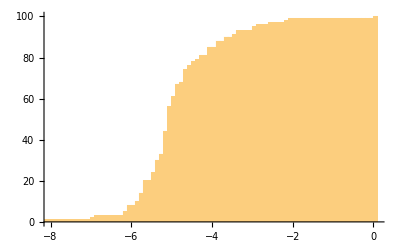

```mathematica
Histogram[Log[Abs[#]]&/@spec,{.1},"CumulativeCount"]
```

```mathematica
hlist=(specAbs=Sort[Log[Abs[#]]&/@spec];Join[{{specAbs_⟦1⟧-1,0}},Transpose[{specAbs,Table[n,{n,1,Length[specAbs]}]}],{{0,Length[specAbs]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-10.7025,0)(-9.70254,1)(-6.97026,2)(-6.83086,3)(-6.17283,4)(-6.13546,5)(-6.05554,6)(-6.02619,7)(-6.02619,8)(-5.88851,9)(-5.88851,10)(-5.78722,11)(-5.78722,12)(-5.73496,13)(-5.73496,14)(-5.62732,15)(-5.62732,16)(-5.61596,17)(-5.61596,18)(-5.60439,19)(-5.60439,20)(-5.49642,21)(-5.49642,22)(-5.44225,23)(-5.44225,24)(-5.39887,25)(-5.39887,26)(-5.39739,27)(-5.39739,28)(-5.33575,29)(-5.33575,30)(-5.28906,31)(-5.21107,32)(-5.21107,33)(-5.15066,34)(-5.15066,35)(-5.14974,36)(-5.14974,37)(-5.14752,38)(-5.14752,39)(-5.13523,40)(-5.13523,41)(-5.13437,42)(-5.13184,43)(-5.13184,44)(-5.08877,45)(-5.08877,46)(-5.06909,47)(-5.06909,48)(-5.06067,49)(-5.06067,50)(-5.04885,51)(-5.04885,52)(-5.02879,53)(-5.02879,54)(-5.00133,55)(-5.00133,56)(-4.986,57)(-4.986,58)(-4.96484,59)(-4.96484,60)(-4.91339,61)(-4.83398,62)(-4.83398,63)(-4.80904,64)(-4.80904,65)(-4.80473,66)(-4.80473,67)(-4.75738,68)(-4.69589,69)(-4.64885,70)(-4.64885,71)(-4.62598,72)(-4.62598,73)(-4.62206,74)(-4.51145,75)(-4.51145,76)(-4.46195,77)(-4.44569,78)(-4.33745,79)(-4.29365,80)(-4.29365,81)(-4.09204,82)(-4.09204,83)(-4.08231,84)(-4.08231,85)(-3.81074,86)(-3.81074,87)(-3.801,88)(-3.60207,89)(-3.60207,90)(-3.40818,91)(-3.35394,92)(-3.35394,93)(-2.93705,94)(-2.90322,95)(-2.81764,96)(-2.53974,97)(-2.16768,98)(-2.08388,99)(0.,100)(0.,100)

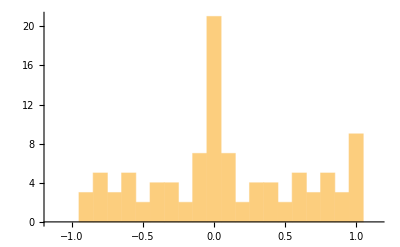

```mathematica
Histogram[Arg[#]/π&/@spec,{-1.15,1.15,.1}]
```

```mathematica
hlist=(specArg=Sort[Arg[#]/π&/@spec];Join[{{-1.15,0}},Transpose[{specArg,Table[n,{n,1,Length[specArg]}]}],{{1.05,Length[specArg]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-1.15,0)(-0.916107,1)(-0.875047,2)(-0.858074,3)(-0.831626,4)(-0.823231,5)(-0.786729,6)(-0.762415,7)(-0.761265,8)(-0.714303,9)(-0.706217,10)(-0.701381,11)(-0.641877,12)(-0.612211,13)(-0.609151,14)(-0.608027,15)(-0.557074,16)(-0.537947,17)(-0.496309,18)(-0.436892,19)(-0.40743,20)(-0.390132,21)(-0.35458,22)(-0.339094,23)(-0.302773,24)(-0.293819,25)(-0.264424,26)(-0.217111,27)(-0.184558,28)(-0.146021,29)(-0.138377,30)(-0.123565,31)(-0.0868932,32)(-0.0862093,33)(-0.0848761,34)(-0.0507398,35)(-0.0406853,36)(-0.0293969,37)(-0.0287539,38)(0.,39)(0.,40)(0.,41)(0.,42)(0.,43)(0.,44)(0.,45)(0.,46)(0.,47)(0.,48)(0.,49)(0.,50)(0.,51)(0.,52)(0.,53)(0.0287539,54)(0.0293969,55)(0.0406853,56)(0.0507398,57)(0.0848761,58)(0.0862093,59)(0.0868932,60)(0.123565,61)(0.138377,62)(0.146021,63)(0.184558,64)(0.217111,65)(0.264424,66)(0.293819,67)(0.302773,68)(0.339094,69)(0.35458,70)(0.390132,71)(0.40743,72)(0.436892,73)(0.496309,74)(0.537947,75)(0.557074,76)(0.608027,77)(0.609151,78)(0.612211,79)(0.641877,80)(0.701381,81)(0.706217,82)(0.714303,83)(0.761265,84)(0.762415,85)(0.786729,86)(0.823231,87)(0.831626,88)(0.858074,89)(0.875047,90)(0.916107,91)(1.,92)(1.,93)(1.,94)(1.,95)(1.,96)(1.,97)(1.,98)(1.,99)(1.,100)(1.05,100)

#### Preparations for [1, Fig. 4]

```mathematica
P=Pfr;
```

```mathematica
rP=#/Max[#]&/@Pfr;
```

```mathematica
Export["Pfr100.txt",StringRiffle[Table["\\put(0,"<>ToString[50-0.5*(i-1)]<>"){"<>StringJoin[Table[prep=ToExpression[ToString[TempRGB[rP_⟦i,j⟧]]];("\\pxl{"<>ToString[prep_⟦1⟧]<>"}{"<>ToString[prep_⟦2⟧]<>"}{"<>ToString[prep_⟦3⟧]<>"}"),{j,1,100}]]<>"}",{i,1,100}],"\n"]]
```

Pfr100.txt

```mathematica
v=Eigenvectors[Transpose[P],1];
```

```mathematica
u=Reverse[Sort[Total[Transpose[#_⟦1⟧]_⟦2⟧]&/@Take[NonStopClustersFrench,100]]]
```

{898,719,564,503,406,358,347,341,291,286,254,254,250,245,233,231,228,227,226,226,212,209,207,201,196,195,194,193,191,179,178,177,172,172,168,166,165,156,154,154,153,149,146,146,142,138,138,137,136,134,134,133,131,130,129,125,124,122,120,119,112,112,108,108,107,107,105,104,102,101,100,100,99,98,98,96,95,93,92,92,91,91,91,91,91,89,89,85,84,84,82,82,81,81,80,80,79,78,78,78}

```mathematica
prep=N[u/Total[u]];StringJoin[Table["("<>ToString[n]<>","<>ToString[prep[[n]]]<>")",{n,1,N0}]]
```

(1,0.0524349)(2,0.0419829)(3,0.0329324)(4,0.0293705)(5,0.0237066)(6,0.0209039)(7,0.0202616)(8,0.0199112)(9,0.0169917)(10,0.0166998)(11,0.0148313)(12,0.0148313)(13,0.0145977)(14,0.0143057)(15,0.013605)(16,0.0134883)(17,0.0133131)(18,0.0132547)(19,0.0131963)(20,0.0131963)(21,0.0123788)(22,0.0122037)(23,0.0120869)(24,0.0117365)(25,0.0114446)(26,0.0113862)(27,0.0113278)(28,0.0112694)(29,0.0111526)(30,0.0104519)(31,0.0103936)(32,0.0103352)(33,0.0100432)(34,0.0100432)(35,0.00980965)(36,0.00969286)(37,0.00963447)(38,0.00910896)(39,0.00899218)(40,0.00899218)(41,0.00893378)(42,0.00870022)(43,0.00852505)(44,0.00852505)(45,0.00829149)(46,0.00805792)(47,0.00805792)(48,0.00799953)(49,0.00794114)(50,0.00782436)(51,0.00782436)(52,0.00776597)(53,0.00764919)(54,0.0075908)(55,0.00753241)(56,0.00729884)(57,0.00724045)(58,0.00712367)(59,0.00700689)(60,0.0069485)(61,0.00653976)(62,0.00653976)(63,0.0063062)(64,0.0063062)(65,0.00624781)(66,0.00624781)(67,0.00613103)(68,0.00607264)(69,0.00595586)(70,0.00589747)(71,0.00583908)(72,0.00583908)(73,0.00578068)(74,0.00572229)(75,0.00572229)(76,0.00560551)(77,0.00554712)(78,0.00543034)(79,0.00537195)(80,0.00537195)(81,0.00531356)(82,0.00531356)(83,0.00531356)(84,0.00531356)(85,0.00531356)(86,0.00519678)(87,0.00519678)(88,0.00496321)(89,0.00490482)(90,0.00490482)(91,0.00478804)(92,0.00478804)(93,0.00472965)(94,0.00472965)(95,0.00467126)(96,0.00467126)(97,0.00461287)(98,0.00455448)(99,0.00455448)(100,0.00455448)

```mathematica
prep=N[v_⟦1⟧/Total[v_⟦1⟧]];StringJoin[Table["("<>ToString[n]<>","<>ToString[prep[[n]]]<>")",{n,1,N0}]]
```

(1,0.0522628)(2,0.0409459)(3,0.0322103)(4,0.0282164)(5,0.0231394)(6,0.0213932)(7,0.0220212)(8,0.0204149)(9,0.0182338)(10,0.0175335)(11,0.0144878)(12,0.0152939)(13,0.0146347)(14,0.0149232)(15,0.0131883)(16,0.0129139)(17,0.0127911)(18,0.0129745)(19,0.0127895)(20,0.0131019)(21,0.0131095)(22,0.0119849)(23,0.0119315)(24,0.0110826)(25,0.0114894)(26,0.0115123)(27,0.0114444)(28,0.0112666)(29,0.0118277)(30,0.0100061)(31,0.0102105)(32,0.0098135)(33,0.00997629)(34,0.0100667)(35,0.00965687)(36,0.00988594)(37,0.00962646)(38,0.00932789)(39,0.00867846)(40,0.00913656)(41,0.00896959)(42,0.00833907)(43,0.00842374)(44,0.00853693)(45,0.00812219)(46,0.00820937)(47,0.00838039)(48,0.0079099)(49,0.00758392)(50,0.00748768)(51,0.00795627)(52,0.00725875)(53,0.00767766)(54,0.00798376)(55,0.00729151)(56,0.00732517)(57,0.00748998)(58,0.00700457)(59,0.0068084)(60,0.00712597)(61,0.00613509)(62,0.00634044)(63,0.00635578)(64,0.00645542)(65,0.00605167)(66,0.0060538)(67,0.00637394)(68,0.00575881)(69,0.00566761)(70,0.00612078)(71,0.00573155)(72,0.0057034)(73,0.0060549)(74,0.00574256)(75,0.0057162)(76,0.00535788)(77,0.00553131)(78,0.0053606)(79,0.00529348)(80,0.00547763)(81,0.00575235)(82,0.00534157)(83,0.00509728)(84,0.00520197)(85,0.00639203)(86,0.00547746)(87,0.00551742)(88,0.00519267)(89,0.00499136)(90,0.00484415)(91,0.00488661)(92,0.00471019)(93,0.00487604)(94,0.00460255)(95,0.00451485)(96,0.00453433)(97,0.00520391)(98,0.00443713)(99,0.00477974)(100,0.00497397)

```mathematica
1/Total[v_⟦1⟧] Sum[v_⟦1,i⟧*P_⟦i,j⟧,{i,1,N0},{j,1,N0}]
```

1.

```mathematica
StringJoin["("<>ToString[#_⟦1⟧]<>","<>ToString[AccountingForm[#_⟦2⟧]]<>")"&/@Table[M=MatrixPower[P,k];{k,1/2 Sum[Abs[1/Total[v_⟦1⟧] v_⟦1,i⟧*M_⟦i,j⟧-1/Total[v_⟦1⟧] v_⟦1,j⟧*M_⟦j,i⟧],{i,1,N0},{j,1,N0}]},{k,1,5}]]
```

(1,0.07244072260401)(2,0.00423860781595)(3,0.00045132032522)(4,0.0000530568982)(5,0.0000063604116)

### Data for topic patterns

```mathematica
TopicClusters=DeleteCases[NonStopClusters,{_,_,_,"B",_,_,_,_}];
```

```mathematica
Length[TopicClusters]
```

176

```mathematica
SelectedClusters=TopicClusters;
```

```mathematica
TopicClustersFrench=TopicClusters;
```

```mathematica
Timing[PfrTopic=Table[Table[prepP=TransitionMeasure[SelectedClusters_⟦m,1⟧,SelectedClusters_⟦n,1⟧,SelectedClusters_⟦m,5⟧,SelectedClusters_⟦m,6⟧],{n,1,Length[SelectedClusters]}],{m,1,Length[SelectedClusters]}];]
```

{91.125,Null}

```mathematica
Timing[PfrT=Table[v=Table[prepP=PfrTopic_⟦m,n⟧;prepP_⟦1⟧*Exp[-prepP_⟦2⟧],{n,1,100}];v/Total[v],{m,1,100}];]
```

{0.046875,Null}

```mathematica
Timing[spec=Eigenvalues[PfrT];]
```

{1.20313,Null}

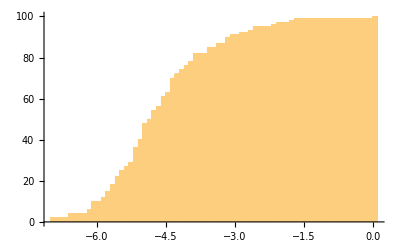

```mathematica
Histogram[Log[Abs[#]]&/@spec,{.1},"CumulativeCount"]
```

```mathematica
hlist=(specAbs=Sort[Log[Abs[#]]&/@spec];Join[{{specAbs_⟦1⟧-1,0}},Transpose[{specAbs,Table[n,{n,1,Length[specAbs]}]}],{{0,Length[specAbs]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-7.98738,0)(-6.98738,1)(-6.98738,2)(-6.58593,3)(-6.58593,4)(-6.19059,5)(-6.19059,6)(-6.05522,7)(-6.05522,8)(-6.00681,9)(-6.00681,10)(-5.82719,11)(-5.82719,12)(-5.7636,13)(-5.70311,14)(-5.70311,15)(-5.64552,16)(-5.64552,17)(-5.62481,18)(-5.5429,19)(-5.5429,20)(-5.53299,21)(-5.53299,22)(-5.49563,23)(-5.44215,24)(-5.44215,25)(-5.35766,26)(-5.35766,27)(-5.29928,28)(-5.29928,29)(-5.19729,30)(-5.19729,31)(-5.17482,32)(-5.17482,33)(-5.10716,34)(-5.10589,35)(-5.10589,36)(-5.09241,37)(-5.09241,38)(-5.04826,39)(-5.04826,40)(-4.94524,41)(-4.94524,42)(-4.91123,43)(-4.91123,44)(-4.90458,45)(-4.90458,46)(-4.90125,47)(-4.90125,48)(-4.80578,49)(-4.80578,50)(-4.78352,51)(-4.78352,52)(-4.72885,53)(-4.72885,54)(-4.65178,55)(-4.65178,56)(-4.5942,57)(-4.5942,58)(-4.55332,59)(-4.55123,60)(-4.55123,61)(-4.46128,62)(-4.46128,63)(-4.36928,64)(-4.34322,65)(-4.34322,66)(-4.33944,67)(-4.33944,68)(-4.30743,69)(-4.30743,70)(-4.24431,71)(-4.24431,72)(-4.12211,73)(-4.12211,74)(-4.08369,75)(-4.08369,76)(-3.95151,77)(-3.95151,78)(-3.89279,79)(-3.89279,80)(-3.81254,81)(-3.81254,82)(-3.5733,83)(-3.5692,84)(-3.5692,85)(-3.37496,86)(-3.37496,87)(-3.19273,88)(-3.19273,89)(-3.12316,90)(-3.02459,91)(-2.80758,92)(-2.69181,93)(-2.58098,94)(-2.54607,95)(-2.19391,96)(-2.05851,97)(-1.79776,98)(-1.68165,99)(0.,100)(0.,100)

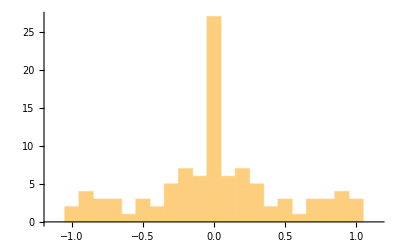

```mathematica
Histogram[Arg[#]/π&/@spec,{-1.15,1.15,.1}]
```

```mathematica
hlist=(specArg=Sort[Arg[#]/π&/@spec];Join[{{-1.15,0}},Transpose[{specArg,Table[n,{n,1,Length[specArg]}]}],{{1.05,Length[specArg]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-1.15,0)(-0.984424,1)(-0.95564,2)(-0.916054,3)(-0.902622,4)(-0.889559,5)(-0.878205,6)(-0.838322,7)(-0.77609,8)(-0.773773,9)(-0.74764,10)(-0.666201,11)(-0.664262,12)(-0.581887,13)(-0.545433,14)(-0.530191,15)(-0.476821,16)(-0.392471,17)(-0.385043,18)(-0.326677,19)(-0.302075,20)(-0.292492,21)(-0.292072,22)(-0.258901,23)(-0.24667,24)(-0.228918,25)(-0.220227,26)(-0.200743,27)(-0.197494,28)(-0.160544,29)(-0.153026,30)(-0.1229,31)(-0.119567,32)(-0.106538,33)(-0.097078,34)(-0.0610466,35)(-0.0607413,36)(-0.0498591,37)(-0.0461557,38)(-0.0444138,39)(-0.0177216,40)(-0.0175389,41)(0.,42)(0.,43)(0.,44)(0.,45)(0.,46)(0.,47)(0.,48)(0.,49)(0.,50)(0.,51)(0.,52)(0.,53)(0.,54)(0.,55)(0.,56)(0.,57)(0.,58)(0.0175389,59)(0.0177216,60)(0.0444138,61)(0.0461557,62)(0.0498591,63)(0.0607413,64)(0.0610466,65)(0.097078,66)(0.106538,67)(0.119567,68)(0.1229,69)(0.153026,70)(0.160544,71)(0.197494,72)(0.200743,73)(0.220227,74)(0.228918,75)(0.24667,76)(0.258901,77)(0.292072,78)(0.292492,79)(0.302075,80)(0.326677,81)(0.385043,82)(0.392471,83)(0.476821,84)(0.530191,85)(0.545433,86)(0.581887,87)(0.664262,88)(0.666201,89)(0.74764,90)(0.773773,91)(0.77609,92)(0.838322,93)(0.878205,94)(0.889559,95)(0.902622,96)(0.916054,97)(0.95564,98)(0.984424,99)(1.,100)(1.05,100)

### Preparations for [1, Fig. 5B]

```mathematica
SelectedTopics=Cases[TopicClustersFrench,{{___,{#,_},___},___}]_⟦1⟧&/@TopicsNamesFrench;
```

```mathematica
KinSpecSWLongTag[TopicClustersFrench,PfrTopic,#_⟦1⟧&/@SelectedTopics]
```

Here are the lists of eigenvalues for the three selected topics:

```mathematica
FrenchKinQ0=KinQ0
```

{{0.98670952648885,0.29046355070285,0.077243920566755,0.070178592622111,0.055800967695906,0.04690052676014,0.032320235971054,0.024523874035401,0.024523874035401,0.024058090248797,0.024058090248797,0.011885566893427,0.011885566893427,0.011508329458327,0.011508329458327,0.0093020338656421,0.0093020338656421,0.0059969921357614,0.0059969921357614,0.0037105307187518,0.0037105307187518,0},{0.87274662498189,0.13402030925592,0.066055151593952,0.060757440303617,0.049779557208906,0.04113072882617,0.034821576251659,0.033805032693716,0.030425216037853,0.030425216037853,0.028954594339425,0.022434070413181,0.022434070413181,0.01894502531524,0.01894502531524,0.017160470087544,0.017160470087544,0.014578656820408,0.014578656820408,0.012325162834233,0.012325162834233,0.01022534985282,0.01022534985282,0.0097030243181894,0.0097030243181894,0.0093433848733112,0.0093433848733112,0.0084557184365678,0.0069966497271836,0.0069966497271836,0.0055272436843553,0.0055272436843553,0.0052328506608351,0.0052328506608351,0.0028466688587721,0.0028466688587721,0},{0.65397441084215,0.14750593818719,0.1005268622625,0.069737607453562,0.069737607453562,0.045316039353679,0.030792990115849,0.022298724779183,0.022298724779183,0.021265235545267,0.020739886126934,0.020739886126934,0.012180248761332,0.012180248761332,0.011956689722765,0.011956689722765,0.011896336477332,0.011347182951063,0.011241650730774,0.011241650730774,0.0043903732264131,0.0043903732264131,0.002582504967977,0.002582504967977,0.0005034507290616,0}}

```mathematica
FrenchKinQ=KinQ
```

{{0.98670952648885,0.29046355070285,0.077243920566755,0.070178592622111,0.055800967695906,0.04690052676014,0.032320235971054,0.024523874035401},{0.87274662498189,0.13402030925592,0.066055151593952,0.060757440303617,0.049779557208906,0.04113072882617,0.034821576251659,0.033805032693716,0.030425216037853,0.030425216037853,0.028954594339425,0.022434070413181,0.022434070413181,0.01894502531524,0.01894502531524,0.017160470087544,0.017160470087544,0.014578656820408},{0.65397441084215,0.14750593818719,0.1005268622625,0.069737607453562,0.069737607453562,0.045316039353679,0.030792990115849,0.022298724779183,0.022298724779183,0.021265235545267,0.020739886126934}}

```mathematica
TopicNames=TopicsNamesFrench
```

{orgueil,darcy,elizabeth}

```mathematica
Cl=TopicClustersFrench;
```

```mathematica
PT=PfrTopic;
```

```mathematica
AffinitySmallWorlds=Table[PT_⟦SeekPos[TopicNames_⟦k⟧,Cl],TopicSmallWorlds_⟦k,j⟧,3⟧,{k,1,Length[TopicNames]},{j,1,Length[TopicSmallWorlds_⟦k⟧]}];
```

```mathematica
SmallWorldWeights=Table[v=Eigenvectors[Transpose[RenormPSW_⟦k⟧],1];prob=v_⟦1⟧/Total[v_⟦1⟧];Table[ReplacePart[Cl_⟦TopicSmallWorlds_⟦k,m⟧⟧,{2->prob_⟦m⟧,5->AffinitySmallWorlds_⟦k,m⟧}],{m,1,Length[RenormPSW_⟦k⟧]}],{k,1,Length[RenormPSW]}];
```

```mathematica
SortWordClusters[list_,ScalingFactor_,MaxClusters_]:=(AllCluster=Take[Sort[(prep=CensorCluster[#_⟦1⟧];{prep,#_⟦2⟧,Total[Transpose[prep]_⟦2⟧],#_⟦4⟧,#_⟦5⟧})&/@list,#1[[2]]>#2[[2]]&],UpTo[MaxClusters]];SizedWords=Table[Width=Total[Max/@StringLength[#_⟦2⟧&/@#&/@SplitEven[EvenOut[Transpose[AllCluster_⟦n,1⟧]]]]];ScalingFactor √(AllCluster_⟦n,2⟧/Width)*{Width*0.95,1/0.9},{n,1,Length[AllCluster]}];)
```

```mathematica
SmallWorldCloudPlot[ScalingFactor_,MaxClusters_,OutputFileName_]:=(FindCenter[SizedWords];MinX=Min[Table[CenterList_⟦n,1⟧-SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MinY=Min[Table[CenterList_⟦n,2⟧-SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];MaxX=Max[Table[CenterList_⟦n,1⟧+SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MaxY=Max[Table[CenterList_⟦n,2⟧+SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];ArrangedCluster=Table[WCCounts=Transpose[SortBy[AllCluster_⟦n,1⟧,First]];{SizedWords_⟦n⟧,WCCounts_⟦1⟧,WCCounts_⟦2⟧,AllCluster_⟦n,3⟧,AllCluster_⟦n,4⟧,CenterList_⟦n⟧,AllCluster_⟦n,5⟧},{n,1,Length[AllCluster]}];str=OpenWrite[OutputFileName];WriteString[str,"\\begin{minipage}{\\textwidth}\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}\\begin{picture}("<>ToString[N[Round[MaxX-MinX,10^-3]]]<>","<>ToString[N[Round[MaxY-MinY,10^-3]]]<>"){\\textbf{"<>StringJoin[Table["\\put("<>ToString[N[Round[ArrangedCluster_⟦k,6,1⟧-ArrangedCluster_⟦k,1,1⟧/2,10^-3]]]<>","<>ToString[N[Round[ArrangedCluster_⟦k,6,2⟧-ArrangedCluster_⟦k,1,2⟧/2,10^-3]]]<>"){\\textcolor[rgb]"<>ToString[RainbowRGB[ArrangedCluster_⟦k,7⟧]]<>"{"<>"
\\setlength{\\unitlength}{"<>ToString[N[Round[0.85*2.54/72 ArrangedCluster_⟦k,1,2⟧,10^-3]]]<>"cm}{
"<>(BCData=Word2BarChart[{ArrangedCluster_⟦k,2⟧,ArrangedCluster_⟦k,3⟧}];H=ArrangedCluster_⟦k,4⟧;StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*0.85 ArrangedCluster_⟦k,1,2⟧*2.54/72<0.01),"","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>(temp=ToUpperCase[BCData_⟦m,n,2⟧];ToString[N[Round[BCData_⟦m,n,3⟧/H*If[temp1=StringReplace[temp,{"Œ":>"OE","Æ":>"AE","Ç":>"C"}];RemoveDiacritics[temp1,Language->"French"]==temp1,1,1.4],10^-3]]])<>"}{"<>(If[StringDelete[temp,CharacterRange["A","Z"]]=="",temp,StringReplace[StringReplace[ExportString[temp,"TeX"],___~~"\\[\\text{":>""],"}\\]"~~___:>""]])<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}}
",{k,1,Length[ArrangedCluster]}]]<>"}}\\end{picture}\\end{spacing}\\end{minipage}"];Close[str];)
```

```mathematica
SortWordClusters[SmallWorldWeights_⟦1⟧,30,Length[SmallWorldWeights_⟦1⟧]];SmallWorldCloudPlot[1,20,"fr-pride.txt"];
```

```mathematica
SortWordClusters[SmallWorldWeights_⟦2⟧,30,Length[SmallWorldWeights_⟦2⟧]];SmallWorldCloudPlot[1,25,"fr-Darcy.txt"];
```

```mathematica
SortWordClusters[SmallWorldWeights_⟦3⟧,30,Length[SmallWorldWeights_⟦3⟧]];SmallWorldCloudPlot[1,25,"fr-Eliza.txt"];
```

### Preparations for [1, Fig. 3c]

#### Bulk vector

```mathematica
EnglishRef=TopicClustersEnglish;
```

```mathematica
FrenchRef=TopicClustersFrench;
```

```mathematica
PandPChapEnglish=StringSplit[ExampleData[{"Text","PrideAndPrejudice"}],"Chapter "~~DigitCharacter..~~" "];
```

```mathematica
Length[PandPChapEnglish]
```

61

```mathematica
VecEnglish=Table[{EnglishRef_⟦k,1⟧,StringCount[PandPChapEnglish,WordBoundary~~Alternatives@@(#_⟦1⟧&/@EnglishRef_⟦k,1⟧)~~WordBoundary,IgnoreCase->True]},{k,1,Length[EnglishRef]}];
```

```mathematica
PandPChapFrench=StringSplit[StringReplace[ImportString[StringReplace[Import["Les cinq filles de Mrs Bennet (Leconte-Pressoir).txt"],{"\n":>"垚"," ?":>"?"," !":>"!"," :":>":"," ;":>";","« ":>"«"," »":>"»"}],"HTML"],"垚":>"\n"],("I"|"V"|"X"|"L")..~~"\n"];
```

```mathematica
Length[PandPChapFrench]
```

61

```mathematica
VecFrench=Table[{FrenchRef_⟦k,1⟧,StringCount[PandPChapFrench,WordBoundary~~Alternatives@@(#_⟦1⟧&/@FrenchRef_⟦k,1⟧)~~WordBoundary,IgnoreCase->True]},{k,1,Length[FrenchRef]}];
```

```mathematica
BulkPairing=Flatten[Table[{#_⟦1⟧,#_⟦2,k⟧},{k,1,Length[#_⟦2⟧]}]&/@Select[Table[{EnglishRef[[k,1]],#_⟦1⟧&/@Select[VecFrench,JaccardRuzickaSim[#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧]≥0.7&]},{k,1,Length[EnglishRef]}],Length[#_⟦2⟧]>0&],1]
```

{{{{Mr,786}},{{messieurs,14},{monsieur,30},{mr,854}}},{{{Eliza,22},{Elizabeth,597},{Elizabeth's,38}},{{eliza,13},{elizabeth,706}}},{{{said,401},{say,160},{saying,35},{says,15}},{{dira,1},{dirai,4},{diraient,1},{dirais,3},{dirait,2},{dire,166},{dirent,2},{direz,1},{dis,13},{disant,7},{disaient,2},{disais,3},{disait,28},{dise,3},{disions,1},{dit,290},{dite,4},{dites,33}}},{{{Darcy,374},{Darcy's,44}},{{darcy,503}}},{{{Mrs,343}},{{mrs,358}}},{{{Bennet,294},{Bennet's,29},{Bennets,10}},{{bennet,341}}},{{{Bingley,257},{Bingley's,49},{Bingleys,4},{Bingleys',1}},{{bingley,347}}},{{{miss,283},{missed,3},{missing,1},{missent,2},{missish,1}},{{mademoiselle,7},{mesdemoiselles,1},{miss,255},{demoiselle,3},{demoiselles,20}}},{{{Jane,263},{Jane's,28}},{{jane,291}}},{{{Wickham,162},{Wickham's,32}},{{wickham,231}}},{{{Collins,156},{Collins's,24}},{{colline,3},{collines,3},{collins,188}}},{{{dear,158},{dearly,3},{dearest,17}},{{cher,33},{chère,90},{chèrement,1},{chères,1},{chérie,13}}},{{{Lydia,133},{Lydia's,38}},{{lydia,191}}},{{{maternal,2},{mother,110},{mother's,25}},{{maman,11},{mère,116},{maternel,1},{maternelles,1},{maternels,1}}},{{{father,116},{father's,19}},{{papa,5},{père,123},{paternel,2},{paternelle,1},{paternels,1},{pères,1}}},{{{letter,115},{letters,16},{letter-paper,1}},{{lettre,126},{lettres,12}}},{{{Catherine,110},{Catherine's,16}},{{catherine,124}}},{{{Gardiner,84},{Gardiner's,13},{Gardiners,6}},{{gardiner,108}}},{{{Lizzy,95},{Lizzy's,2}},{{lizzy,89}}},{{{write,39},{writes,1},{writing,12},{written,19},{writer,3},{wrote,21}},{{écrirai,1},{écrirait,1},{écrire,24},{écrirez,1},{écriront,1},{écris,3},{écrit,12},{écrite,6},{écrites,2},{écrivant,1},{écrivait,3},{écrive,1},{écrivez,7},{écrivis,1},{écrivit,9},{écrivît,1},{écriture,4}}},{{{aunt,78},{aunt's,6},{aunts,1}},{{tante,81},{tantes,1}}},{{{Charlotte,68},{Charlotte's,17}},{{charlotte,91}}},{{{Lucas,65},{Lucas's,5},{Lucases,13},{Lucases',1}},{{lucas,78}}},{{{brother,62},{brotherly,2},{brother's,13},{brothers,2}},{{frère,81},{fraternel,3},{fraternelle,5}}},{{{Netherfield,73}},{{netherfield,66}}},{{{dance,31},{danced,12},{dances,10},{dancing,21}},{{danse,15},{dansé,6},{dansent,1},{danser,17},{dansera,1},{danserai,1},{danserait,1},{danses,6},{danseur,2},{danseurs,8},{danseuse,11},{danseuses,3}}},{{{uncle,59},{uncle's,9},{uncles,3}},{{oncle,71},{oncles,2}}},{{{Kitty,69},{Kitty's,2}},{{kitty,57}}},{{{colonel,65},{colonel's,1}},{{colonel,66}}},{{{cousin,41},{cousin's,8},{cousins,11}},{{cousin,33},{cousine,29},{cousines,11},{cousins,4}}},{{{Meryton,57}},{{meryton,56}}},{{{Pemberley,53}},{{pemberley,55}}},{{{Rosings,49}},{{rosings,43}}},{{{week,29},{weeks,18}},{{semaine,24},{semaines,15}}},{{{William,40},{William's,6}},{{sir,44}}},{{{William,40},{William's,6}},{{william,43}}},{{{Forster,38},{Forster's,1},{Forsters,1}},{{forster,40}}},{{{Mary,38},{Mary's,1}},{{mary,36}}},{{{Bourgh,35},{Bourgh's,4}},{{bourgh,37}}},{{{de,39}},{{bourgh,37}}},{{{Fitzwilliam,32},{Fitzwilliam's,5}},{{fitzwilliam,37}}},{{{Hurst,32},{Hurst's,1},{Hursts,1}},{{hurst,38}}},{{{Phillip's,1},{Phillips,26},{Phillips's,5}},{{philips,33}}},{{{niece,20},{niece's,2},{nieces,9}},{{nièce,32},{nièces,9}}},{{{nephew,20},{nephew's,2},{nephews,2}},{{neveu,28},{neveux,3}}},{{{Derbyshire,24}},{{derbyshire,23}}},{{{Brighton,24}},{{brighton,23}}}}

```mathematica
SiftedTags=Union[(#_⟦1⟧&/@BulkPairing)];SiftedEnglishRef=Reverse[SortBy[Table[Cases[EnglishRef,{SiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[SiftedTags]}],#_⟦3⟧&]];
```

```mathematica
SiftedTags=Union[(#_⟦2⟧&/@BulkPairing)];SiftedFrenchRef=Reverse[SortBy[Table[Cases[FrenchRef,{SiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[SiftedTags]}],#_⟦3⟧&]];
```

```mathematica
Length[SiftedEnglishRef]
```

46

```mathematica
Length[SiftedFrenchRef]
```

46

```mathematica
BulkSim=Flatten[Table[{k,j,JaccardRuzickaSim[Cases[VecFrench,{SiftedFrenchRef[[j,1]],___}]_⟦1,2⟧,Cases[VecEnglish,{SiftedEnglishRef[[k,1]],___}]_⟦1,2⟧]},{k,1,Length[SiftedEnglishRef]},{j,1,Length[SiftedFrenchRef]}],1];
```

```mathematica
OptimalNodes={Position[SiftedEnglishRef,{#_⟦1⟧,___}]_⟦1,1⟧,Position[SiftedFrenchRef,{#_⟦2⟧,___}]_⟦1,1⟧}&/@BulkPairing;
```

```mathematica
Export["Fig3D.txt","%tournament\n"<>StringJoin[Riffle[Flatten["\\put("<>ToString[1.5+1+4#_⟦2⟧]<>","<>ToString[90-4#_⟦1⟧]<>"){\\color[rgb]"<>ToString[TempRGB[N[#_⟦3⟧]]]<>"{\\rule{4pt}{4pt}}}"&/@BulkSim],"\n"]]<>"\n\n%crosshairs\n"<>StringJoin[Riffle["\n%"<>SiftedEnglishRef[[#_⟦1⟧,1,1,1]]<>"_"<>SiftedFrenchRef[[#_⟦2⟧,1,1,1]]<>"
\\put("<>ToString[1.5+4#_⟦2⟧+3]<>","<>ToString[90-4#_⟦1⟧+2]<>"){\\color{green}\\linethickness{"<>ToString[1]<>"pt}\\line(-1,0){"<>ToString[4#_⟦2⟧-2]<>"}\\linethickness{"<>ToString[1]<>"pt}\\line(0,1){"<>ToString[4#_⟦1⟧-2]<>"}}"&/@OptimalNodes,"\n"]]];
```

#### English labels

```mathematica
FromClusters=SiftedEnglishRef;
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@((prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@FromClusters);
```

```mathematica
EnglishCompress[w_]:=StringReplace[w,{"ai":>"𝔸","ea":>"𝕀","ou":>"𝕌","ee":>"𝔼","oo":>"𝕆"}]
```

```mathematica
EnglishDecompress[w_]:=StringReplace[w,{"𝔸":>"ai","𝕀":>"ea","𝕌":>"ou","𝔼":>"ee","𝕆":>"oo"}]
```

```mathematica
EvenOut[cl_]:=(prep=EnglishCompress[cl_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,cl_⟦2⟧}])
```

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,EnglishDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Export["EnglishLabels_Fig3c.txt",StringJoin[Table[(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\put("<>ToString[5-3Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[91.75-1.5-4k]<>"){"<>"\\textbf{"<>"\\setlength{\\unitlength}{3pt}"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*3<0.15),"","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}\n",{k,1,Length[ScoredCluster]}]]];
```

#### French labels

```mathematica
FromClusters=SiftedFrenchRef;
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@((prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@FromClusters);
```

```mathematica
EvenOut[cl_]:=(prep=cl_⟦1⟧;L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,cl_⟦2⟧}])
```

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,StringTake[#_⟦1⟧,{m}],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
ClusterCount={{"France","Français","François"},{10,72,83}}
```

{{France,Français,François},{10,72,83}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
CumHeight[(ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]])_⟦3⟧]
```

{{{6},o,83,0},{{6},a,72,83},{{6},e,10,155}}

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Export["FrenchLabels_Fig3c.txt",StringJoin[Table[(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\put("<>ToString[5.25-.25+1+4k]<>","<>ToString[91]<>"){"<>"\\textbf{"<>"\\setlength{\\unitlength}{3pt}"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*3<0.15),"","\\BCR{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>(temp=ToUpperCase[BCData_⟦m,n,2⟧];ToString[N[Round[BCData_⟦m,n,3⟧/H*If[temp1=StringReplace[temp,{"Œ":>"OE","Æ":>"AE","Ç":>"C"}];RemoveDiacritics[temp1,Language->"French"]==temp1,1,1.4],10^-3]]])<>"}{"<>(If[StringDelete[temp,CharacterRange["A","Z"]]=="",temp,StringReplace[StringReplace[ExportString[temp,"TeX"],___~~"\\[\\text{":>""],"}\\]"~~___:>""]])<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}\n",{k,1,Length[ScoredCluster]}]]];
```

### Preparations for [1, Fig. 6]

#### Bulk vectors

```mathematica
EnglishRef=TopicClustersEnglish;
```

```mathematica
FrenchRef=TopicClustersFrench;
```

```mathematica
PandPChapEnglish=StringSplit[ExampleData[{"Text","PrideAndPrejudice"}],"Chapter "~~DigitCharacter..~~" "];
```

```mathematica
Length[PandPChapEnglish]
```

61

```mathematica
VecEnglish=Table[{EnglishRef_⟦k,1⟧,StringCount[PandPChapEnglish,WordBoundary~~Alternatives@@(#_⟦1⟧&/@EnglishRef_⟦k,1⟧)~~WordBoundary,IgnoreCase->True]},{k,1,Length[EnglishRef]}];
```

```mathematica
PandPChapFrench=StringSplit[StringReplace[ImportString[StringReplace[Import["Les cinq filles de Mrs Bennet (Leconte-Pressoir).txt"],{"\n":>"垚"," ?":>"?"," !":>"!"," :":>":"," ;":>";","« ":>"«"," »":>"»"}],"HTML"],"垚":>"\n"],("I"|"V"|"X"|"L")..~~"\n"];
```

```mathematica
Length[PandPChapFrench]
```

61

```mathematica
VecFrench=Table[{FrenchRef_⟦k,1⟧,StringCount[PandPChapFrench,WordBoundary~~Alternatives@@(#_⟦1⟧&/@FrenchRef_⟦k,1⟧)~~WordBoundary,IgnoreCase->True]},{k,1,Length[FrenchRef]}];
```

```mathematica
FlatScreenedPairs=Flatten[Table[{#_⟦1⟧,#_⟦2,k⟧},{k,1,Length[#_⟦2⟧]}]&/@Select[Table[{EnglishRef[[k,1]],#_⟦1⟧&/@Select[VecFrench,JaccardRuzickaSim[#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧]≥Max[1-7/100*√61,1-√(Length[Select[Min[#]&/@Transpose[{#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧}],#>0&]]/Total[Max[#]&/@Transpose[{#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧}]])]&]},{k,1,Length[EnglishRef]}],Length[#_⟦2⟧]>0&],1];
```

```mathematica
SiftedTags=Union[(#_⟦1⟧&/@FlatScreenedPairs)];SiftedEnglishRef=Reverse[SortBy[Table[Cases[EnglishRef,{SiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[SiftedTags]}],#_⟦3⟧&]];
```

```mathematica
SiftedTags=Union[(#_⟦2⟧&/@FlatScreenedPairs)];SiftedFrenchRef=Reverse[SortBy[Table[Cases[FrenchRef,{SiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[SiftedTags]}],#_⟦3⟧&]];
```

```mathematica
Length[SiftedEnglishRef]
```

93

```mathematica
Length[SiftedFrenchRef]
```

88

#### Spectral parameters for English

```mathematica
FromTopics=SiftedEnglishRef;
```

```mathematica
FromDelta=ReadDelta[#]&/@FromTopics;
```

```mathematica
FromN=(#_⟦3⟧-1)&/@FromTopics;
```

```mathematica
AbsoluteTiming[KinSpecSWLongTag[TopicClustersEnglish,PenTopic,#_⟦1⟧&/@FromTopics];]
```

{49.4077,Null}

```mathematica
FromKinQ=KinQ;
```

```mathematica
FromEta=SemanticComplexities;
```

#### Spectral parameters for French

```mathematica
ToTopicsFrench=SiftedFrenchRef;
```

```mathematica
Length[ToTopicsFrench]
```

88

```mathematica
ToDeltaFrench=ReadDelta[#]&/@ToTopicsFrench;
```

```mathematica
ToNFrench=(#_⟦3⟧-1)&/@ToTopicsFrench;
```

```mathematica
AbsoluteTiming[KinSpecSWLongTag[TopicClustersFrench,PfrTopic,#_⟦1⟧&/@ToTopicsFrench];]
```

{29.3798,Null}

```mathematica
ToKinFrench=KinQ;
```

```mathematica
ToEtaFrench=SemanticComplexities;
```

#### Translation

```mathematica
AbsoluteTiming[fromLabeled=Transpose[{#_⟦1⟧&/@FromTopics,FromKinQ}];toLabeled=Transpose[{#_⟦1⟧&/@ToTopicsFrench,ToKinFrench}];Report=Table[{FlatScreenedPairs_⟦k⟧,(JaccardRuzickaSim[Cases[fromLabeled,{FlatScreenedPairs_⟦k,1⟧,_}]_⟦1,2⟧,Cases[toLabeled,{FlatScreenedPairs_⟦k,2⟧,_}]_⟦1,2⟧])},{k,1,Length[FlatScreenedPairs]}];]
```

{0.0152283,Null}

```mathematica
prep=Union[Select[Table[{Report_⟦n,1,1⟧,Report_⟦n,1,2⟧,Report_⟦n,2⟧},{n,1,Length[Report]}],#_⟦3⟧≥0.7&]];g=Graph[(#_⟦1⟧->#_⟦2⟧)&/@prep,EdgeWeight->(#_⟦3⟧&/@prep)];(KuhnSln={#,FindRowRank[#,prep],FindColRank[#,prep]}&/@Select[{#,PropertyValue[{g,#},EdgeWeight]}&/@FindIndependentEdgeSet[g],#_⟦2⟧>0&])//TableForm
```

{{Brighton,24}}->{{brighton,23}}
0.91219392803447 | 1 | 1
{{Bourgh,35},{Bourgh's,4}}->{{bourgh,37}}
0.90034041636299 | 1 | 1
{{Derbyshire,24}}->{{derbyshire,23}}
0.89498240626145 | 1 | 1
{{impossible,44}}->{{impossible,36},{impossibilité,4}}
0.78102307794038 | 1 | 1
{{town,64}}->{{londres,99}}
0.8993490642447 | 1 | 1
{{Meryton,57}}->{{meryton,56}}
0.87017751264949 | 1 | 1
{{Mr,786}}->{{messieurs,14},{monsieur,30},{mr,854}}
0.8114582266476 | 1 | 1
{{Mrs,343}}->{{mrs,358}}
0.86567576390308 | 1 | 1
{{Netherfield,73}}->{{netherfield,66}}
0.83627776514922 | 1 | 1
{{park,22}}->{{parc,24}}
0.8059099518775 | 1 | 1
{{Pemberley,53}}->{{pemberley,55}}
0.89714891894131 | 1 | 1
{{Rosings,49}}->{{rosings,43}}
0.85465270734946 | 1 | 1
{{sir,78}}->{{sir,44}}
0.88790506059179 | 1 | 2
{{thousand,34}}->{{mille,39},{milles,14},{millar,1}}
0.7764321541869 | 1 | 1
{{two,135}}->{{deux,207}}
0.86045543276454 | 1 | 1
{{absence,27},{absent,4}}->{{absentât,1},{absente,2},{absenter,1},{absent,2},{absence,22}}
0.74509703347519 | 1 | 1
{{ball,34},{balls,8}}->{{bal,38},{bals,6}}
0.83375190648669 | 1 | 1
{{Catherine,110},{Catherine's,16}}->{{catherine,124}}
0.82240987372605 | 1 | 1
{{Charlotte,68},{Charlotte's,17}}->{{charlotte,91}}
0.89943297959311 | 1 | 1
{{Collins,156},{Collins's,24}}->{{colline,3},{collines,3},{collins,188}}
0.87205294982585 | 1 | 1
{{colonel,65},{colonel's,1}}->{{colonel,66}}
0.84789109550398 | 1 | 1
{{Darcy,374},{Darcy's,44}}->{{darcy,503}}
0.88775402460433 | 1 | 1
{{dinner,33},{dinners,2}}->{{dînaient,1},{dîné,4},{dînent,1},{dîner,45},{dînerait,1},{dînèrent,2},{dîners,2},{dînons,1}}
0.82503274620274 | 1 | 1
{{distance,16},{distant,5}}->{{distancée,1},{distante,2},{distancer,1},{distancèrent,1},{distances,2},{distant,1},{distance,18}}
0.7940871012092 | 1 | 1
{{father,116},{father's,19}}->{{papa,5},{père,123},{paternel,2},{paternelle,1},{paternels,1},{pères,1}}
0.92328262837858 | 1 | 1
{{Fitzwilliam,32},{Fitzwilliam's,5}}->{{fitzwilliam,37}}
0.90601451267444 | 1 | 1
{{ignorance,7},{ignorant,16}}->{{ignorante,1},{ignorantes,3},{ignorance,7},{ignoraient,1},{ignorais,2},{ignorait,3},{ignore,13},{ignoré,1},{ignorées,1},{ignorer,7},{ignorés,1},{ignorez,1},{ignorons,1}}
0.92114609452499 | 1 | 1
{{Jane,263},{Jane's,28}}->{{jane,291}}
0.90758640664858 | 1 | 1
{{Kitty,69},{Kitty's,2}}->{{kitty,57}}
0.87295994720587 | 1 | 1
{{Lizzy,95},{Lizzy's,2}}->{{lizzy,89}}
0.87759802356985 | 1 | 1
{{Lydia,133},{Lydia's,38}}->{{lydia,191}}
0.9369503728182 | 1 | 1
{{Mary,38},{Mary's,1}}->{{mary,36}}
0.82372975539019 | 1 | 1
{{poor,38},{poorly,3}}->{{pauvre,28},{pauvres,4},{pauvreté,3}}
0.84104094560698 | 1 | 1
{{regiment,19},{regiment's,3}}->{{régiment,29}}
0.75584074163956 | 1 | 1
{{societies,1},{society,33}}->{{social,1},{sociale,3},{sociales,2},{sociable,1},{société,31},{sociétés,2}}
0.85860385699929 | 1 | 1
{{table,28},{tables,3}}->{{table,27},{tables,4}}
0.74968688569715 | 1 | 1
{{ten,33},{tens,1}}->{{dix,22}}
0.75080542889254 | 1 | 1
{{week,29},{weeks,18}}->{{semaine,24},{semaines,15}}
0.72441719988836 | 1 | 1
{{Wickham,162},{Wickham's,32}}->{{wickham,231}}
0.77914331857406 | 1 | 1
{{William,40},{William's,6}}->{{william,43}}
0.87291678147802 | 2 | 1
{{aunt,78},{aunt's,6},{aunts,1}}->{{tante,81},{tantes,1}}
0.84030858639098 | 1 | 1
{{Bennet,294},{Bennet's,29},{Bennets,10}}->{{bennet,341}}
0.84665090223434 | 1 | 1
{{child,14},{children,25},{childhood,1}}->{{enfance,6},{enfant,19},{enfants,23}}
0.8654107168352 | 1 | 1
{{cousin,41},{cousin's,8},{cousins,11}}->{{cousin,33},{cousine,29},{cousines,11},{cousins,4}}
0.84346134860668 | 1 | 1
{{cried,91},{cry,1},{crying,2}}->{{écria,65},{écriait,1},{écriant,1}}
0.8396426652619 | 1 | 1
{{dear,158},{dearly,3},{dearest,17}}->{{cher,33},{chère,90},{chèrement,1},{chères,1},{chérie,13}}
0.87667533371077 | 1 | 1
{{Eliza,22},{Elizabeth,597},{Elizabeth's,38}}->{{eliza,13},{elizabeth,706}}
0.79209738219418 | 1 | 1
{{evening,72},{evening's,2},{evenings,4}}->{{soir,52},{soirée,49},{soirées,3},{soirs,1}}
0.82186833652264 | 1 | 1
{{invite,6},{invited,11},{inviting,3},{invitation,34},{invitations,1}}->{{invita,2},{invitait,1},{invitant,1},{invite,1},{invité,4},{invitée,8},{inviter,14},{invités,6},{invitation,35},{invitations,7}}
0.88175025703713 | 1 | 1
{{eye,15},{eyeing,1},{eyes,52}}->{{œil,23},{yeux,68}}
0.82758607221079 | 1 | 1
{{Forster,38},{Forster's,1},{Forsters,1}}->{{forster,40}}
0.88807088320422 | 1 | 1
{{Gardiner,84},{Gardiner's,13},{Gardiners,6}}->{{gardiner,108}}
0.79136959593944 | 1 | 1
{{husband,42},{husband's,8},{husbands,4}}->{{mari,52},{maris,3}}
0.90826824745417 | 1 | 1
{{letter,115},{letters,16},{letter-paper,1}}->{{lettre,126},{lettres,12}}
0.89548764645551 | 1 | 1
{{maternal,2},{mother,110},{mother's,25}}->{{maman,11},{mère,116},{maternel,1},{maternelles,1},{maternels,1}}
0.90368440979329 | 1 | 1
{{motion,1},{motive,17},{motives,7}}->{{motif,16},{motifs,12},{motivé,1}}
0.90909081392852 | 1 | 1
{{nephew,20},{nephew's,2},{nephews,2}}->{{neveu,28},{neveux,3}}
0.87074822159735 | 1 | 1
{{niece,20},{niece's,2},{nieces,9}}->{{nièce,32},{nièces,9}}
0.82149227594481 | 1 | 1
{{Phillip's,1},{Phillips,26},{Phillips's,5}}->{{philips,33}}
0.91223501156644 | 1 | 1
{{polite,5},{politely,3},{politeness,17}}->{{poli,1},{polie,1},{poliment,3},{polis,1},{politesse,34}}
0.88363318951406 | 1 | 1
{{uncle,59},{uncle's,9},{uncles,3}}->{{oncle,71},{oncles,2}}
0.8050618702029 | 1 | 1
{{year,28},{years,33},{years',2}}->{{an,9},{ans,31},{année,6},{années,15}}
0.87890156289266 | 1 | 1
{{young,130},{younger,30},{youngest,13}}->{{jeune,117},{jeunes,96},{jeunesse,13}}
0.7275390460135 | 1 | 1
{{best,41},{better,92},{good,184},{good-humoured,6}}->{{bon,44},{bons,8},{meilleur,10},{meilleurs,5},{mieux,94},{bonne,59},{bonnes,18},{meilleure,11},{meilleures,5}}
0.76870497782776 | 1 | 1
{{Bingley,257},{Bingley's,49},{Bingleys,4},{Bingleys',1}}->{{bingley,347}}
0.84919713483974 | 1 | 1
{{brother,62},{brotherly,2},{brother's,13},{brothers,2}}->{{frère,81},{fraternel,3},{fraternelle,5}}
0.89495759181294 | 1 | 1
{{fortune,39},{fortunes,1},{fortunate,15},{fortunately,2}}->{{fortune,40},{fortuné,1}}
0.81027765703131 | 1 | 1
{{Lucas,65},{Lucas's,5},{Lucases,13},{Lucases',1}}->{{lucas,78}}
0.89435139568821 | 1 | 1
{{promise,17},{promised,21},{promises,3},{promising,4}}->{{promesse,20},{promesses,1},{promet,1},{promets,3},{promettant,2},{promettaient,1},{promettait,4},{promettez,1},{promettre,3}}
0.70796663445094 | 1 | 1
{{send,24},{sending,1},{sends,1},{sent,20}}->{{enverrai,2},{envoie,2},{envoya,2},{envoyé,9},{envoyée,3},{envoyer,17},{envoyez,2}}
0.87719142305864 | 1 | 1
{{carriage,44},{carriages,6},{carried,8},{carry,5},{carrying,4}}->{{voiture,50},{voitures,2}}
0.74615227478601 | 1 | 1
{{congratulate,7},{congratulated,2},{congratulation,1},{congratulations,12},{congratulatory,1}}->{{félicita,7},{félicitait,3},{félicitant,2},{félicite,2},{félicité,9},{féliciter,5},{félicitations,12}}
0.84289368544475 | 1 | 1
{{ladies,74},{lady,183},{lady's,8},{ladyship,30},{ladyship's,12}}->{{lady,136},{madame,20},{dame,13},{dames,43}}
0.80241450914801 | 1 | 1
{{laugh,18},{laughed,11},{laughing,10},{laughingly,2},{laughter,2}}->{{ri,2},{riant,4},{riaient,1},{riait,1},{riez,2},{rire,17},{ris,3},{risée,1},{rit,1}}
0.75738645782512 | 1 | 1
{{miss,283},{missed,3},{missing,1},{missent,2},{missish,1}}->{{mademoiselle,7},{mesdemoiselles,1},{miss,255},{demoiselle,3},{demoiselles,20}}
0.85740912612456 | 1 | 1
{{refuse,9},{refused,6},{refusing,7},{refusal,7},{refusals,1}}->{{refus,15},{refusa,3},{refusais,1},{refusait,1},{refusant,3},{refuse,2},{refusé,5},{refusée,2},{refuser,11},{refuserais,2},{refuserait,1},{refusez,4}}
0.87765087666623 | 1 | 1
{{feel,39},{feeling,38},{feelingly,1},{feelings,86},{feels,4},{felt,100}}->{{sensibilité,3},{sentant,4},{sentaient,6},{sentais,2},{sentait,16},{sentez,2},{senti,5},{sentier,6},{sentir,13},{sentirai,1},{sentirent,1},{sentirez,1},{sentit,18},{sentît,1},{sentiments,78},{sentiment,44}}
0.72385920794117 | 1 | 1
{{marriage,66},{married,61},{marry,42},{marrying,23},{matrimonial,1},{matrimony,6}}->{{mariant,1},{mariait,1},{marie,1},{marié,3},{mariée,19},{mariées,4},{marierait,1},{mariés,9},{marient,2},{marier,28},{marieraient,1},{mariez,1},{mariage,95}}
0.90387813521302 | 1 | 1
{{office,6},{officer,8},{officers,29},{officers',2},{officiousness,1},{officious,3}}->{{office,3},{officier,12},{officiers,23},{officiels,1},{officiellement,1}}
0.71450818422525 | 1 | 1
{{visit,51},{visited,4},{visiting,5},{visits,5},{visitor,11},{visitors,14}}->{{visitait,1},{visite,57},{visité,2},{visiter,12},{visites,10},{visiteur,3},{visiteurs,11},{visiteuse,2},{visiteuses,3}}
0.77440677709631 | 1 | 1
{{write,39},{writes,1},{writing,12},{written,19},{writer,3},{wrote,21}}->{{écrirai,1},{écrirait,1},{écrire,24},{écrirez,1},{écriront,1},{écris,3},{écrit,12},{écrite,6},{écrites,2},{écrivant,1},{écrivait,3},{écrive,1},{écrivez,7},{écrivis,1},{écrivit,9},{écrivît,1},{écriture,4}}
0.93029265592712 | 1 | 1
{{thank,19},{thanked,7},{thankful,8},{thankfully,1},{thankfulness,1},{thanking,4},{thanks,14}}->{{remercia,5},{remerciant,1},{remercie,9},{remerciée,1},{remercier,9},{remercierais,1},{remerciez,1},{remerciements,10}}
0.79675998802125 | 1 | 1

```mathematica
ResiftedTags=Union[(#_⟦1⟧&/@prep)];ResiftedEnglishRef=Reverse[SortBy[Table[Cases[EnglishRef,{ResiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[ResiftedTags]}],#_⟦3⟧&]];
```

```mathematica
ResiftedTags=Union[(#_⟦2⟧&/@prep)];ResiftedFrenchRef=Reverse[SortBy[Table[Cases[FrenchRef,{ResiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[ResiftedTags]}],#_⟦3⟧&]];
```

```mathematica
SemanticSim={Position[ResiftedEnglishRef,{#_⟦1⟧,___}]_⟦1,1⟧,Position[ResiftedFrenchRef,{#_⟦2⟧,___}]_⟦1,1⟧,#_⟦3⟧}&/@prep;
```

```mathematica
OptimalNodes={Position[ResiftedEnglishRef,{#_⟦1,1,1⟧,___}]_⟦1,1⟧,Position[ResiftedFrenchRef,{#_⟦1,1,2,1⟧,___}]_⟦1,1⟧,#_⟦2,1,1⟧,#_⟦3,1,1⟧}&/@KuhnSln;
```

```mathematica
Export["Fig6.txt","%tournament\n"<>StringJoin[Riffle[Flatten["\\put("<>ToString[1.5+1+4#_⟦2⟧]<>","<>ToString[90-4#_⟦1⟧]<>"){\\color[rgb]"<>ToString[TempRGB[#_⟦3⟧]]<>"{\\rule{4pt}{4pt}}}"&/@SemanticSim],"\n"]]<>"\n%crosshairs\n"<>StringJoin[Riffle["\n%"<>ResiftedEnglishRef[[#_⟦1⟧,1,1,1]]<>"_"<>ResiftedFrenchRef[[#_⟦2⟧,1,1,1]]<>"
\\put("<>ToString[1.5+4#_⟦2⟧+3]<>","<>ToString[90-4#_⟦1⟧+2]<>"){\\color{green}\\linethickness{"<>ToString[1.5/#_⟦3⟧]<>"pt}\\line(-1,0){"<>ToString[4#_⟦2⟧-2]<>"}\\linethickness{"<>ToString[1.5/#_⟦4⟧]<>"pt}\\line(0,1){"<>ToString[4#_⟦1⟧-2]<>"}}"&/@OptimalNodes,"\n"]]];
```

#### English labels

```mathematica
FromClusters=ResiftedEnglishRef;
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@((prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@FromClusters);
```

```mathematica
EnglishCompress[w_]:=StringReplace[w,{"ai":>"𝔸","ea":>"𝕀","ou":>"𝕌","ee":>"𝔼","oo":>"𝕆"}]
```

```mathematica
EnglishDecompress[w_]:=StringReplace[w,{"𝔸":>"ai","𝕀":>"ea","𝕌":>"ou","𝔼":>"ee","𝕆":>"oo"}]
```

```mathematica
EvenOut[cl_]:=(prep=EnglishCompress[cl_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,cl_⟦2⟧}])
```

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,EnglishDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Export["EnglishLabels_Fig6.txt",StringJoin[Table[(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\put("<>ToString[5-3Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[91.75-1.5-4k]<>"){"<>"\\textbf{"<>"\\setlength{\\unitlength}{3pt}"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*3<0.15),"","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}\n",{k,1,Length[ScoredCluster]}]]];
```

#### French labels

```mathematica
FromClusters=ResiftedFrenchRef;
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@((prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@FromClusters);
```

```mathematica
EvenOut[cl_]:=(prep=cl_⟦1⟧;L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,cl_⟦2⟧}])
```

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,StringTake[#_⟦1⟧,{m}],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
ClusterCount={{"France","Français","François"},{10,72,83}}
```

{{France,Français,François},{10,72,83}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
CumHeight[(ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]])_⟦3⟧]
```

{{{6},o,83,0},{{6},a,72,83},{{6},e,10,155}}

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Export["FrenchLabels_Fig6.txt",StringJoin[Table[(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\put("<>ToString[5.25-.25+1+4k]<>","<>ToString[91]<>"){"<>"\\textbf{"<>"\\setlength{\\unitlength}{3pt}"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*3<0.15),"","\\BCR{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>(temp=ToUpperCase[BCData_⟦m,n,2⟧];ToString[N[Round[BCData_⟦m,n,3⟧/H*If[temp1=StringReplace[temp,{"Œ":>"OE","Æ":>"AE","Ç":>"C"}];RemoveDiacritics[temp1,Language->"French"]==temp1,1,1.4],10^-3]]])<>"}{"<>(If[StringDelete[temp,CharacterRange["A","Z"]]=="",temp,StringReplace[StringReplace[ExportString[temp,"TeX"],___~~"\\[\\text{":>""],"}\\]"~~___:>""]])<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}\n",{k,1,Length[ScoredCluster]}]]];
```

```mathematica
Export["EnglishFrench_Report.txt",{Last[SortBy[#_⟦1,1,1⟧,Last]]_⟦1⟧,Last[SortBy[#_⟦1,1,2⟧,Last]]_⟦1⟧}&/@KuhnSln];
```